# Phaseshift method applied to PW Wilson line

## Import packages

```mathematica
AppendTo[$Path,ToFileName[{NotebookDirectory[]}]<>"Packages"];
<<WKB`
<<phaseShiftSolver`
<<commons`
<<operatorsWL.m
```

## Equations to solve, initialization cell

```mathematica
beq=dotApply[opY,({{ϕ1[σ]}, {ϕ2[σ]}})]//Flatten
(*feq=dotApply[({{(m-λ+V[σ])#&, fL[#,σ]&}, {fLBar[#,σ]&, (m+λ)#&}}),({{ψ1[σ]}, {ψ2[σ]}})]//Flatten*)
feq=dotApply[opF,({{ψ1[σ]}, {ψ2[σ]}})]//Flatten
```

{(m-λ+V[σ]) ϕ1[σ]-((1+2 σ^2) A[σ] ϕ2[σ])/(2 σ √(-1+σ^2))-√(-1+σ^2) A[σ] ϕ2'[σ],-((-4 σ+(-1+4 σ^2) A[σ]) ϕ1[σ])/(2 σ √(-1+σ^2))+(m+λ) ϕ2[σ]-√(-1+σ^2) A[σ] ϕ1'[σ]}

{(m+λ) ψ1[σ]+((1+2 σ^2) A[σ] ψ2[σ])/(2 σ √(-1+σ^2))+√(-1+σ^2) A[σ] ψ2'[σ],((-4 σ+(-1+4 σ^2) A[σ]) ψ1[σ])/(2 σ √(-1+σ^2))+(m-λ+V[σ]) ψ2[σ]+√(-1+σ^2) A[σ] ψ1'[σ]}

### Version as in the paper

Differences between my operator (H_x) and the one in the paper (H_k): -σ_3 . time reversal
	H_x=(1-λ | -L1
-L2 | 1+λ)         
		↕ -σ_3 (-σ_3M σ_3)=M σ_3	
	H_k=(1-λ | L1
-L2 | -1-λ)

```mathematica
opY
```

{{(m-λ+V[σ]) #1&,-fL1[#1,σ]&},{-fL2[#1,σ]&,(m+λ) #1&}}

```mathematica
opY.PauliMatrix[3]
```

{{(m-λ+V[σ]) #1&,-(-fL1[#1,σ]&)},{-fL2[#1,σ]&,-((m+λ) #1&)}}

Differences between my operator (H_x) and the one in the paper (H_k):
	H_x=(1+λ | L1
L2 | 1-λ)         <----  σ_1 M σ_1  ---->	 (H̃)_x=(1-λ | L2
L1 | 1+λ)
		↕?						↕   -σ_3 (-σ_3M σ_3)=M σ_3	
	H_k=(-1-λ | L1
-L2 | 1-λ)	 <----  σ_1 M σ_1  ---->        (H̃)_k=(1-λ | -L2
L1 | -1-λ)
So, in order to obtain the desired transformation, we compose:
	H_k=σ_1(H̃)_k σ_1= σ_1(H̃)_x σ_3 σ_1= σ_1 σ_1 H_x σ_1 σ_3 σ_1=-H_x σ_3

```mathematica
opF
```

{{(m+λ) #1&,fL1[#1,σ]&},{fL2[#1,σ]&,(m-λ+V[σ]) #1&}}

```mathematica
-opF.PauliMatrix[3]
```

{{-((m+λ) #1&),fL1[#1,σ]&},{-(fL2[#1,σ]&),(m-λ+V[σ]) #1&}}

## Asymptotics of the equations

### Close to boundary behavior to fix the initial conditions

We expand the wave functions close to boundary and fix the exponents by imposing the equations to vanish at leading order.

#### Boson ϕ[σ]≈(σ-1)^(1/4)(1 0)+(σ-1)^(3/4)(0 -1/3 √2 (-2+λ))+O((σ-1)^(5/4))

```mathematica
op=opY;

Print[Style["Expand the operator to the leading order:",Red]]
1/(σ-1)^ν dotApply[op,(σ-1)^ν({{C1}, {C2}})]//Simplify//Flatten;
SeriesCoefficient[#,-1/2]&/@Series[%/.potentialRule/.explicitARule,{σ,1,0}]
Flatten[Solve[#==0,ν]&/@%,1]
dotApply[op,(σ-1)^ν({{C1}, {C2}})]/.%;
Normal/@Series[#/.potentialRule/.explicitARule,{σ,1,0}]&@%//Simplify
Solve[#=={0,0},{C1,C2}]&/@%
Print[Style["For the solution ν=-3/4 to be zero, C1=C2=0, for ν=1/4 solution, we require C2=0, and C1 arbitrary, so we choose it to be 1.",Red]]

Print[Style["Next-to-leading order for the normalizable solution:",Red]]
dotApply[op,(σ-1)^(1/4)({{1}, {0}})+(σ-1)^(3/4)({{C1}, {C2}})];
SeriesCoefficient[#,0]&/@Series[%/.potentialRule/.explicitARule,{σ,1,1}]//Simplify
SeriesCoefficient[#,1/4]&@@@%
Solve[%==0,{C1,C2}]
```

Expand the operator to the leading order:

{-(3 C2)/(2 √2)-√2 C2 ν,C1/(2 √2)-√2 C1 ν}

{{ν→-3/4},{ν→1/4}}

{{{(-8 C1 (-2+λ)+√2 C2 √(-1+σ))/(8 (-1+σ)^(3/4))},{(√2 C1 (17-9 σ)+8 C2 (1+λ) √(-1+σ))/(8 (-1+σ)^(5/4))}},{{-(√2 C2)/(-1+σ)^(1/4)},{0}}}

Solve::svars: Equations may not give solutions for all "solve" variables.

{{{C1→0,C2→0}},{{C2→0}}}

For the solution ν=-3/4 to be zero, C1=C2=0, for ν=1/4 solution, we require C2=0, and C1 arbitrary, so we choose it to be 1.

Next-to-leading order for the normalizable solution:

{{(2-(3 C2)/(√2)-λ) (σ-1)^(1/4)-C1 (-2+λ) (σ-1)^(3/4)+O[σ-1]^(5/4)},{-(C1 (σ-1)^(1/4))/(√2)+(C2 (1+λ)+(-19+Log[256])/(4 √2)-√2 Log[-1+σ]) (σ-1)^(3/4)+O[σ-1]^(5/4)}}

{2-(3 C2)/(√2)-λ,-C1/(√2)}

{{C1→0,C2→-1/3 √2 (-2+λ)}}

#### Fermion ψ[σ]≈(σ-1)^(1/4)(1 0)+(σ-1)^(3/4)(0 -1/3 √2 (1+λ))+O((σ-1)^(5/4))

```mathematica
op=opF;

Print[Style["Expand the operator to the leading order:",Red]]
1/(σ-1)^ν dotApply[op,(σ-1)^ν({{C1}, {C2}})]//Simplify//Flatten;
SeriesCoefficient[#,-1/2]&/@Series[%/.potentialRule/.explicitARule,{σ,1,0}]
Flatten[Solve[#==0,ν]&/@%,1]
dotApply[op,(σ-1)^ν({{C1}, {C2}})]/.%;
Normal/@Series[#/.potentialRule/.explicitARule,{σ,1,0}]&@%//Simplify
Solve[#=={0,0},{C1,C2}]&/@%
Print[Style["For the solution ν=-3/4 to be zero, C1=C2=0, for ν=1/4 solution, we require C2=0, and C1 arbitrary, so we choose it to be 1.",Red]]

Print[Style["Next-to-leading order for the normalizable solution:",Red]]
dotApply[op,(σ-1)^(1/4)({{1}, {0}})+(σ-1)^(3/4)({{C1}, {C2}})];
SeriesCoefficient[#,0]&/@Series[%/.potentialRule/.explicitARule,{σ,1,1}]//Simplify
SeriesCoefficient[#,1/4]&@@@%
Solve[%==0,{C1,C2}]
```

Expand the operator to the leading order:

{(3 C2)/(2 √2)+√2 C2 ν,-C1/(2 √2)+√2 C1 ν}

{{ν→-3/4},{ν→1/4}}

{{{(C1 (1+λ))/(-1+σ)^(3/4)-C2/(4 √2 (-1+σ)^(1/4))},{(-8 C2 (-2+λ) √(-1+σ)+√2 C1 (-17+9 σ))/(8 (-1+σ)^(5/4))}},{{(√2 C2)/(-1+σ)^(1/4)},{0}}}

Solve::svars: Equations may not give solutions for all "solve" variables.

{{{C1→0,C2→0}},{{C2→0}}}

For the solution ν=-3/4 to be zero, C1=C2=0, for ν=1/4 solution, we require C2=0, and C1 arbitrary, so we choose it to be 1.

Next-to-leading order for the normalizable solution:

{{(1+(3 C2)/(√2)+λ) (σ-1)^(1/4)+(C1+C1 λ) (σ-1)^(3/4)+O[σ-1]^(5/4)},{(C1 (σ-1)^(1/4))/(√2)+(-C2 (-2+λ)+(19-8 Log[2])/(4 √2)+√2 Log[-1+σ]) (σ-1)^(3/4)+O[σ-1]^(5/4)}}

{1+(3 C2)/(√2)+λ,C1/(√2)}

{{C1→0,C2→-1/3 √2 (1+λ)}}

### Asymptotic behavior

We are solving the 2 leading orders!

```mathematica
beq/.potentialRule/.explicitARule;
beqL=Normal@Series[%,{σ,∞,0}]//FullSimplify 

feq/.potentialRule/.explicitARule;
feqL=Normal@Series[%,{σ,∞,0}]//FullSimplify
```

{-(-1+λ) ϕ1[σ]-(2 (ϕ2[σ]+σ ϕ2'[σ]))/(3 σ),(2 ϕ1[σ])/(3 σ)+(1+λ) ϕ2[σ]-(2 ϕ1'[σ])/3}

{(1+λ) ψ1[σ]+(2 (ψ2[σ]+σ ψ2'[σ]))/(3 σ),-(2 ψ1[σ])/(3 σ)+ψ2[σ]-λ ψ2[σ]+(2 ψ1'[σ])/3}

```mathematica
toPureFunction[Rule[y_[x_],expr_]]:=Module[{},
y->Function[x,#]&@expr
]
```

#### Boson: ϕ1= Sin[p σ - p] ϕ2=2/(3 (1±λ) σ)(p σ Cos[p σ-p]-Sin[p σ-p])

```mathematica
(*eqL={-(-1+λ) ϕ1[σ]+(2 ϕ2'[σ])/3,(1+λ) ϕ2[σ]+(2 ϕ1'[σ])/3};*)
eqL=beqL;
X={ϕ1,ϕ2};

r1=Solve[eqL[[2]]==0,X[[2]][σ]]//Flatten
eqL[[1]]/.toPureFunction[Sequence@@%]//Simplify
r2=DSolve[%==0&&X[[1]][1]==0/.λ->√((2/3p)^2+1),X[[1]][σ],σ]//PowerExpand//FullSimplify//Flatten
%/.C[1]-> -1/Csc[p]
r1/.toPureFunction[Sequence@@%]
Clear[X,eqL,r1,r2]
```

{ϕ2[σ]→-(2 (ϕ1[σ]-σ ϕ1'[σ]))/(3 (1+λ) σ)}

-(9 (-1+λ^2) ϕ1[σ]+4 ϕ1''[σ])/(9 (1+λ))

{ϕ1[σ]→C[1] Csc[p] Sin[p-p σ]}

{ϕ1[σ]→-Sin[p-p σ]}

{ϕ2[σ]→-(2 (-p σ Cos[p-p σ]-Sin[p-p σ]))/(3 (1+λ) σ)}

```mathematica
Sin[-x]==-Sin[x]
Cos[-x]==Cos[x]
```

True

True

Absorb a sign:
	ϕ1= Sin[p σ - p]
ϕ2=2/(3 (1±λ) σ)(-p σ Cos[p σ-p]+Sin[p σ-p])

#### Fermion ψ1= Sin[p σ - p] ψ2=2/(3 (-1±λ) σ)(p σ Cos[p σ-p]-Sin[p σ-p])

```mathematica
eqL=feqL;
X={ψ1,ψ2};

r1=Solve[eqL[[2]]==0,X[[2]][σ]]//Flatten
eqL[[1]]/.toPureFunction[Sequence@@%]//Simplify
r2=DSolve[%==0&&X[[1]][1]==0/.λ->√((2/3p)^2+1),X[[1]][σ],σ]//PowerExpand//Simplify//Flatten
%/.C[1]-> -1/Csc[p]
r1/.toPureFunction[Sequence@@%]
Clear[X,eqL,r1,r2]
```

{ψ2[σ]→-(2 (ψ1[σ]-σ ψ1'[σ]))/(3 (-1+λ) σ)}

(9 (-1+λ^2) ψ1[σ]+4 ψ1''[σ])/(9 (-1+λ))

{ψ1[σ]→C[1] Csc[p] Sin[p-p σ]}

{ψ1[σ]→-Sin[p-p σ]}

{ψ2[σ]→-(2 (-p σ Cos[p-p σ]-Sin[p-p σ]))/(3 (-1+λ) σ)}

## WKB analysis

δ[p]=∫_1^σ S'[σ']ⅆσ'
δ[p]=p δ_0+1/p δ_1+...

We will use effective modes for the components, since WKB code is for 2nd order ODEs only.
ω should be replaced by ⅈλ, according to the derivation in the phase-shift method (see package).

### Limits: WKB vs Boundary vs Phase-shift

WKB regime: p >> 1

Close boundary regime: σ-1<<1

Phase-shift limit: σ - 1>>1 and  p (σ - 1) >> 1

Hence, WKB regime is compatible with close to boundary regime and the phase-shift method.

### As 2nd order operators: yeff1, yeff2, feff1, feff2, and its close to boundary behavior

```mathematica
firstODEsToSecondODE[matrixOperator_?MatrixQ,x_?notNumericQ][Y1_,Y2_]:=Module[{V1,V2,D1,D2},
({{V1, D1}, {D2, V2}})=matrixOperator;
{-D1[1/V2[1] D2[Y1]]+V1[Y1],-D2[1/V1[1] D1[Y2]]+V2[Y2]}
]
```

#### Bosonic mode 0={(m+λ) (m-λ+V[σ])+(A[σ] (16 σ^3+ (3+6 σ^2-24 σ^4) A[σ] ))/(4 σ^2 (-1+σ^2))}ϕ1[σ]+2 A[σ] (2-3 σ A[σ]) ϕ1'[σ]-(-1+σ^2) A[σ]^2 ϕ1''[σ] 0={(m+λ) (m-λ+V[σ])+(A[σ] (8 σ +16 σ^3+(-1+2 σ^2-16 σ^4) A[σ] ))/(4 σ^2 (-1+σ^2))+((1+2 σ^2) A[σ]^2 V'[σ])/(2 σ (m-λ+V[σ]))}ϕ1[σ]+{2 A[σ] (2-3 σ A[σ]) +((-1+σ^2) A[σ]^2 V'[σ])/(m-λ+V[σ])} ϕ1'[σ]-(-1+σ^2) A[σ]^2 ϕ1''[σ]

```mathematica
(* Bosonic y operator *)
op=opY;vector={ϕ1[σ],ϕ2[σ]};
firstODEsToSecondODE[op,σ][vector[[1]],vector[[2]]];
yeff1=Collect[%[[1]](m+λ)/.ARule,derivList[vector[[1]],2],Simplify]
yeff2=Collect[%%[[2]](m-λ+V[σ])/.ARule,derivList[vector[[2]],2],Simplify]
```

((16 σ^3 A[σ]+(3+6 σ^2-24 σ^4) A[σ]^2+4 (m+λ) σ^2 (-1+σ^2) (m-λ+V[σ])) ϕ1[σ])/(4 σ^2 (-1+σ^2))+2 A[σ] (2-3 σ A[σ]) ϕ1'[σ]-(-1+σ^2) A[σ]^2 ϕ1''[σ]

1/(4 σ^2 (-1+σ^2) (m-λ+V[σ]))ϕ2[σ] (8 σ (1+2 σ^2) A[σ] (m-λ+V[σ])+4 (m+λ) σ^2 (-1+σ^2) (m-λ+V[σ])^2-A[σ]^2 ((m-λ) (1-2 σ^2+16 σ^4)+(1-2 σ^2+16 σ^4) V[σ]+2 σ (1+σ^2-2 σ^4) V'[σ]))+(A[σ] (4 (m-λ+V[σ])-A[σ] (6 (m-λ) σ+6 σ V[σ]-(-1+σ^2) V'[σ])) ϕ2'[σ])/(m-λ+V[σ])-(-1+σ^2) A[σ]^2 ϕ2''[σ]

```mathematica
Clear[p]
ϕ1[τ_]:= (τ-1)^p
1/ϕ1[σ] Series[yeff1/.potentialRule/.explicitARule,{σ,1,0}]//FullSimplify 
Solve[0==Numerator@Normal@%,p]
ϕ2[τ_]:= (τ-1)^p
1/ϕ2[σ] Series[yeff2/.potentialRule/.explicitARule,{σ,1,0}]//FullSimplify 
Solve[0==Numerator@Normal@%,p]
Clear[ϕ1,ϕ2]
```

(1/8-2 p^2)/(σ-1)+O[σ-1]^0

{{p→-1/4},{p→1/4}}

(9/8-2 p^2)/(σ-1)+O[σ-1]^0

{{p→-3/4},{p→3/4}}

#### Fermionic mode 0={(m+λ) (m-λ+V[σ])+(A[σ] (16 σ^3+ (3+6 σ^2-24 σ^4) A[σ] ))/(4 σ^2 (-1+σ^2))+((-4 σ+(-1+4 σ^2) A[σ])A[σ] V'[σ])/(2σ(m-λ+V[σ]))}ψ1[σ]+{2 A[σ] (2-3 σ A[σ]) +((-1+σ^2) A[σ]^2 V'[σ])/(m-λ+V[σ])}ψ1'[σ]-(-1+σ^2) A[σ]^2 ψ1''[σ] 0={(m+λ) (m-λ+V[σ])+(A[σ] (8 σ +16 σ^3+(-1+2 σ^2-16 σ^4) A[σ] ))/(4 σ^2 (-1+σ^2))}ψ2[σ]+2 A[σ] (2-3 σ A[σ]) ψ2'[σ]-(-1+σ^2) A[σ]^2 ψ2''[σ]

```mathematica
(* Fermionic operator *)
op=opF;vector={ψ1[σ],ψ2[σ]};
firstODEsToSecondODE[op,σ][vector[[1]],vector[[2]]];
feff1=Collect[%[[1]](m-λ+V[σ])/.ARule,derivList[vector[[1]],2],Simplify]
feff2=Collect[%%[[2]](m+λ)/.ARule,derivList[vector[[2]],2],Simplify]
```

1/(4 σ^2 (-1+σ^2) (m-λ+V[σ]))ψ1[σ] (4 (m+λ) σ^2 (-1+σ^2) (m-λ+V[σ])^2+8 σ^2 A[σ] (2 (m-λ) σ+2 σ V[σ]-(-1+σ^2) V'[σ])+A[σ]^2 (-3 (m-λ) (-1-2 σ^2+8 σ^4)+(3+6 σ^2-24 σ^4) V[σ]+2 (σ-5 σ^3+4 σ^5) V'[σ]))+(A[σ] (4 (m-λ+V[σ])-A[σ] (6 (m-λ) σ+6 σ V[σ]-(-1+σ^2) V'[σ])) ψ1'[σ])/(m-λ+V[σ])-(-1+σ^2) A[σ]^2 ψ1''[σ]

((8 (σ+2 σ^3) A[σ]+(-1+2 σ^2-16 σ^4) A[σ]^2+4 (m+λ) σ^2 (-1+σ^2) (m-λ+V[σ])) ψ2[σ])/(4 σ^2 (-1+σ^2))+2 A[σ] (2-3 σ A[σ]) ψ2'[σ]-(-1+σ^2) A[σ]^2 ψ2''[σ]

```mathematica
Clear[p]
ψ1[τ_]:= (τ-1)^p
1/ψ1[σ] Series[feff1/.potentialRule/.explicitARule,{σ,1,0}]//FullSimplify 
Solve[0==Numerator@Normal@%,p]
ψ2[τ_]:= (τ-1)^p
1/ψ2[σ] Series[feff2/.potentialRule/.explicitARule,{σ,1,0}]//FullSimplify 
Solve[0==Numerator@Normal@%,p]
Clear[ψ1,ψ2]
```

(1/8-2 p^2)/(σ-1)+O[σ-1]^0

{{p→-1/4},{p→1/4}}

(9/8-2 p^2)/(σ-1)+O[σ-1]^0

{{p→-3/4},{p→3/4}}

### WKB solutions

Here we choose only one of the 2 solutions from WKB, corresponding to e^S+e^-S which should combined to cosine or sine.

```mathematica
opForm[eq_,wave_[σ_]][ϕ_]:=Coefficient[eq,derivList[wave[σ],2]].{ϕ,D[ϕ,σ],D[ϕ,{σ,2}]}
```

Unfortunately, WKBsolutions doesn’t scale well with the order (76’’ for n=4, 11000’’ for n=6). 
We will export the expressions in a .txt file.

#### 1st components: n=6

```mathematica
n=6;
e=√((2/3 p)^2+m^2);
Timing[y1P6=WKBsolutions[n][opForm[yeff1/.λ-> e,ϕ1[σ]][#]&, {p}][σ]/.potentialRule/.ARule//Simplify]
Timing[y1N6=WKBsolutions[n][opForm[yeff1/.λ->- e,ϕ1[σ]][#]&, {p}][σ]/.potentialRule/.ARule//Simplify]
Timing[f1P6=WKBsolutions[n][opForm[feff1/.λ-> e,ψ1[σ]][#]&, {p}][σ]/.potentialRule/.ARule//Simplify]
Timing[f1N6=WKBsolutions[n][opForm[feff1/.λ->- e,ψ1[σ]][#]&, {p}][σ]/.potentialRule/.ARule//Simplify]
```

{11497.2,{{S0'[σ]→(2 p)/(3 √(-1+σ^2) A[σ]),S1'[σ]→(2 ⅈ σ-3 ⅈ σ^2 A[σ]+√(-1+σ^2) A[σ])/(2 σ A[σ]-2 σ^3 A[σ]),S2'[σ]→(3 (-4 σ^2+4 (σ+ⅈ σ √(-1+σ^2)) A[σ]+(-2+3 σ^4-2 ⅈ √(-1+σ^2)+σ^2 (-1-2 ⅈ √(-1+σ^2))) A[σ]^2))/(16 p σ^2 (-1+σ^2)^(3/2) A[σ]),S3'[σ]→1/(64 p^2 σ^3 (-1+σ^2)^2)9 (-4 σ^2 (2 ⅈ-2 √(-1+σ^2)+σ^2 (-2 ⅈ+√(-1+σ^2)))+4 σ (2 ⅈ-3 ⅈ σ^4-2 √(-1+σ^2)+σ^2 (ⅈ-2 √(-1+σ^2))) A[σ]+(12 ⅈ σ^6+σ^2 √(-1+σ^2)+2 (-ⅈ+√(-1+σ^2))+σ^4 (-10 ⅈ+9 √(-1+σ^2))) A[σ]^2),S4'[σ]→1/(1024 p^3 σ^4 (-1+σ^2)^(5/2) A[σ])27 (-16 σ^4+32 σ^3 (-1-ⅈ √(-1+σ^2)+σ^2 (2+ⅈ √(-1+σ^2))) A[σ]+8 σ^2 (10+10 ⅈ √(-1+σ^2)+σ^4 (-23-2 ⅈ √(-1+σ^2))+σ^2 (11+16 ⅈ √(-1+σ^2))) A[σ]^2+8 σ (-6+54 σ^6-6 ⅈ √(-1+σ^2)+σ^2 (5+2 ⅈ √(-1+σ^2))+σ^4 (-53-44 ⅈ √(-1+σ^2))) A[σ]^3+(8-4 σ^2-297 σ^8+8 ⅈ √(-1+σ^2)+10 σ^6 (35+24 ⅈ √(-1+σ^2))+σ^4 (-57-56 ⅈ √(-1+σ^2))) A[σ]^4),S5'[σ]→1/(4096 p^4 σ^5 (-1+σ^2)^(5/2))81 (16 σ^8-64 σ^3 (-2+σ^4-2 ⅈ √(-1+σ^2)+σ^2 (-9-10 ⅈ √(-1+σ^2))) A[σ]+8 σ^2 (-20+9 σ^6-20 ⅈ √(-1+σ^2)+σ^2 (46+36 ⅈ √(-1+σ^2))+σ^4 (-321-368 ⅈ √(-1+σ^2))) A[σ]^2+(-8+4 σ^2-8 ⅈ √(-1+σ^2)+σ^4 (9+8 ⅈ √(-1+σ^2))+2 σ^6 (557+600 ⅈ √(-1+σ^2))+σ^8 (-2079-2448 ⅈ √(-1+σ^2))) A[σ]^4+8 σ A[σ]^3 (2 (4+4 ⅈ √(-1+σ^2)+σ^2 (-5-3 ⅈ √(-1+σ^2))+σ^4 (-84-93 ⅈ √(-1+σ^2))+σ^6 (247+248 ⅈ √(-1+σ^2)))-ⅈ σ^4 (-1+σ^2)^(9/2) A^(5)[σ])),S6'[σ]→1/(32768 p^5 σ^6 (-1+σ^2)^(7/2) A[σ])243 (-64 σ^6+64 σ^5 (-1-ⅈ √(-1+σ^2)-ⅈ σ^4 √(-1+σ^2)+σ^2 (4+2 ⅈ √(-1+σ^2))) A[σ]+16 σ^4 (-14-14 ⅈ √(-1+σ^2)+2 ⅈ σ^6 √(-1+σ^2)+σ^4 (301+30 ⅈ √(-1+σ^2))+σ^2 (-299-306 ⅈ √(-1+σ^2))) A[σ]^2+32 σ^3 (22+22 ⅈ √(-1+σ^2)+σ^6 (-1120-44 ⅈ √(-1+σ^2))+σ^2 (-219-208 ⅈ √(-1+σ^2))+σ^4 (1319+1022 ⅈ √(-1+σ^2))) A[σ]^3+(-16+50139 σ^12-16 ⅈ √(-1+σ^2)+8 σ^2 (3+2 ⅈ √(-1+σ^2))+σ^4 (-86-80 ⅈ √(-1+σ^2))+σ^6 (-3529-3568 ⅈ √(-1+σ^2))+σ^8 (42943+36192 ⅈ √(-1+σ^2))+σ^10 (-89475-44064 ⅈ √(-1+σ^2))) A[σ]^6-4 σ^2 A[σ]^4 (136 (1+ⅈ √(-1+σ^2))+σ^8 (-17369-240 ⅈ √(-1+σ^2))+σ^2 (-620-552 ⅈ √(-1+σ^2))+σ^4 (-10325-9176 ⅈ √(-1+σ^2))+σ^6 (28178+21928 ⅈ √(-1+σ^2))+88 σ^4 (-1+σ^2)^5 A^(5)[σ])+4 σ A[σ]^5 (40-100 σ^2+219 σ^4-18014 σ^6+38051 σ^8-20196 σ^10+40 ⅈ √(-1+σ^2)-80 ⅈ σ^2 √(-1+σ^2)+504 ⅈ σ^4 √(-1+σ^2)-14608 ⅈ σ^6 √(-1+σ^2)+23936 ⅈ σ^8 √(-1+σ^2)+4 σ^4 (-1+σ^2)^5 (33 σ^2-5 ⅈ √(-1+σ^2)) A^(5)[σ]+4 σ^5 (-1+σ^2)^6 A^(6)[σ]))},{S0'[σ]→-(2 p)/(3 √(-1+σ^2) A[σ]),S1'[σ]→(2 ⅈ σ-3 ⅈ σ^2 A[σ]-√(-1+σ^2) A[σ])/(2 σ A[σ]-2 σ^3 A[σ]),S2'[σ]→(3 (4 σ^2+4 ⅈ σ (ⅈ+√(-1+σ^2)) A[σ]+(2-3 σ^4-2 ⅈ √(-1+σ^2)+σ^2 (1-2 ⅈ √(-1+σ^2))) A[σ]^2))/(16 p σ^2 (-1+σ^2)^(3/2) A[σ]),S3'[σ]→1/(64 p^2 σ^3 (-1+σ^2)^2)9 (4 σ^2 (-2 (ⅈ+√(-1+σ^2))+σ^2 (2 ⅈ+√(-1+σ^2)))+4 σ (-3 ⅈ σ^4+2 (ⅈ+√(-1+σ^2))+σ^2 (ⅈ+2 √(-1+σ^2))) A[σ]-(-12 ⅈ σ^6+σ^2 √(-1+σ^2)+2 (ⅈ+√(-1+σ^2))+σ^4 (10 ⅈ+9 √(-1+σ^2))) A[σ]^2),S4'[σ]→1/(1024 p^3 σ^4 (-1+σ^2)^(5/2) A[σ])27 (16 σ^4+32 σ^3 (1-ⅈ √(-1+σ^2)+ⅈ σ^2 (2 ⅈ+√(-1+σ^2))) A[σ]+8 σ^2 (σ^4 (23-2 ⅈ √(-1+σ^2))+σ^2 (-11+16 ⅈ √(-1+σ^2))+10 ⅈ (ⅈ+√(-1+σ^2))) A[σ]^2-8 σ (-6+54 σ^6+6 ⅈ √(-1+σ^2)+σ^2 (5-2 ⅈ √(-1+σ^2))+σ^4 (-53+44 ⅈ √(-1+σ^2))) A[σ]^3+(-8+4 σ^2+297 σ^8+8 ⅈ √(-1+σ^2)+σ^4 (57-56 ⅈ √(-1+σ^2))+σ^6 (-350+240 ⅈ √(-1+σ^2))) A[σ]^4),S5'[σ]→1/(4096 p^4 σ^5 (-1+σ^2)^(5/2))81 (-16 σ^8+64 σ^3 (-2+σ^4+2 ⅈ √(-1+σ^2)+σ^2 (-9+10 ⅈ √(-1+σ^2))) A[σ]-8 σ^2 (9 σ^6+σ^2 (46-36 ⅈ √(-1+σ^2))+σ^4 (-321+368 ⅈ √(-1+σ^2))+20 ⅈ (ⅈ+√(-1+σ^2))) A[σ]^2+(8-4 σ^2-8 ⅈ √(-1+σ^2)+σ^4 (-9+8 ⅈ √(-1+σ^2))+9 σ^8 (231-272 ⅈ √(-1+σ^2))+2 ⅈ σ^6 (557 ⅈ+600 √(-1+σ^2))) A[σ]^4+8 σ A[σ]^3 (2 (-4+4 ⅈ √(-1+σ^2)+σ^2 (5-3 ⅈ √(-1+σ^2))+σ^4 (84-93 ⅈ √(-1+σ^2))+σ^6 (-247+248 ⅈ √(-1+σ^2)))-ⅈ σ^4 (-1+σ^2)^(9/2) A^(5)[σ])),S6'[σ]→1/(32768 p^5 σ^6 (-1+σ^2)^(7/2) A[σ])243 (64 σ^6+64 σ^5 (1-ⅈ √(-1+σ^2)-ⅈ σ^4 √(-1+σ^2)+2 ⅈ σ^2 (2 ⅈ+√(-1+σ^2))) A[σ]+16 σ^4 (14-14 ⅈ √(-1+σ^2)+2 ⅈ σ^6 √(-1+σ^2)+σ^4 (-301+30 ⅈ √(-1+σ^2))+σ^2 (299-306 ⅈ √(-1+σ^2))) A[σ]^2+32 σ^3 (4 σ^6 (280-11 ⅈ √(-1+σ^2))+σ^2 (219-208 ⅈ √(-1+σ^2))+σ^4 (-1319+1022 ⅈ √(-1+σ^2))+22 ⅈ (ⅈ+√(-1+σ^2))) A[σ]^3+(16-50139 σ^12-16 ⅈ √(-1+σ^2)+σ^4 (86-80 ⅈ √(-1+σ^2))+σ^6 (3529-3568 ⅈ √(-1+σ^2))+σ^8 (-42943+36192 ⅈ √(-1+σ^2))+σ^10 (89475-44064 ⅈ √(-1+σ^2))+8 ⅈ σ^2 (3 ⅈ+2 √(-1+σ^2))) A[σ]^6+4 σ^2 A[σ]^4 (136 (1-ⅈ √(-1+σ^2))+σ^8 (-17369+240 ⅈ √(-1+σ^2))+σ^2 (-620+552 ⅈ √(-1+σ^2))+σ^4 (-10325+9176 ⅈ √(-1+σ^2))+σ^6 (28178-21928 ⅈ √(-1+σ^2))+88 σ^4 (-1+σ^2)^5 A^(5)[σ])-4 σ A[σ]^5 (40-100 σ^2+219 σ^4-18014 σ^6+38051 σ^8-20196 σ^10-40 ⅈ √(-1+σ^2)+80 ⅈ σ^2 √(-1+σ^2)-504 ⅈ σ^4 √(-1+σ^2)+14608 ⅈ σ^6 √(-1+σ^2)-23936 ⅈ σ^8 √(-1+σ^2)+4 σ^4 (-1+σ^2)^5 (33 σ^2+5 ⅈ √(-1+σ^2)) A^(5)[σ]+4 σ^5 (-1+σ^2)^6 A^(6)[σ]))}}}

{11744.7,{{S0'[σ]→-(2 p)/(3 √(-1+σ^2) A[σ]),S1'[σ]→(2 ⅈ σ-3 ⅈ σ^2 A[σ]+√(-1+σ^2) A[σ])/(2 σ A[σ]-2 σ^3 A[σ]),S2'[σ]→(3 (4 σ^2-4 ⅈ σ (-ⅈ+√(-1+σ^2)) A[σ]+(2-3 σ^4+2 ⅈ √(-1+σ^2)+σ^2 (1+2 ⅈ √(-1+σ^2))) A[σ]^2))/(16 p σ^2 (-1+σ^2)^(3/2) A[σ]),S3'[σ]→1/(64 p^2 σ^3 (-1+σ^2)^2)9 (-4 σ^2 (2 ⅈ-2 √(-1+σ^2)+σ^2 (-2 ⅈ+√(-1+σ^2)))+4 σ (2 ⅈ-3 ⅈ σ^4-2 √(-1+σ^2)+σ^2 (ⅈ-2 √(-1+σ^2))) A[σ]+(12 ⅈ σ^6+σ^2 √(-1+σ^2)+2 (-ⅈ+√(-1+σ^2))+σ^4 (-10 ⅈ+9 √(-1+σ^2))) A[σ]^2),S4'[σ]→1/(1024 p^3 σ^4 (-1+σ^2)^(5/2) A[σ])27 (16 σ^4+32 σ^3 (1+ⅈ √(-1+σ^2)+σ^2 (-2-ⅈ √(-1+σ^2))) A[σ]+8 σ^2 (-10-10 ⅈ √(-1+σ^2)+σ^4 (23+2 ⅈ √(-1+σ^2))+σ^2 (-11-16 ⅈ √(-1+σ^2))) A[σ]^2-8 σ (-6+54 σ^6-6 ⅈ √(-1+σ^2)+σ^2 (5+2 ⅈ √(-1+σ^2))+σ^4 (-53-44 ⅈ √(-1+σ^2))) A[σ]^3+(-8+4 σ^2+297 σ^8-8 ⅈ √(-1+σ^2)+σ^4 (57+56 ⅈ √(-1+σ^2))+σ^6 (-350-240 ⅈ √(-1+σ^2))) A[σ]^4),S5'[σ]→1/(4096 p^4 σ^5 (-1+σ^2)^(5/2))81 (16 σ^8-64 σ^3 (-2+σ^4-2 ⅈ √(-1+σ^2)+σ^2 (-9-10 ⅈ √(-1+σ^2))) A[σ]+8 σ^2 (-20+9 σ^6-20 ⅈ √(-1+σ^2)+σ^2 (46+36 ⅈ √(-1+σ^2))+σ^4 (-321-368 ⅈ √(-1+σ^2))) A[σ]^2+(-8+4 σ^2-8 ⅈ √(-1+σ^2)+σ^4 (9+8 ⅈ √(-1+σ^2))+2 σ^6 (557+600 ⅈ √(-1+σ^2))+σ^8 (-2079-2448 ⅈ √(-1+σ^2))) A[σ]^4+8 σ A[σ]^3 (2 (4+4 ⅈ √(-1+σ^2)+σ^2 (-5-3 ⅈ √(-1+σ^2))+σ^4 (-84-93 ⅈ √(-1+σ^2))+σ^6 (247+248 ⅈ √(-1+σ^2)))-ⅈ σ^4 (-1+σ^2)^(9/2) A^(5)[σ])),S6'[σ]→1/(32768 p^5 σ^6 (-1+σ^2)^(7/2) A[σ])243 (64 σ^6+64 σ^5 (1+ⅈ √(-1+σ^2)+ⅈ σ^4 √(-1+σ^2)+σ^2 (-4-2 ⅈ √(-1+σ^2))) A[σ]+16 σ^4 (14+14 ⅈ √(-1+σ^2)-2 ⅈ σ^6 √(-1+σ^2)+σ^4 (-301-30 ⅈ √(-1+σ^2))+σ^2 (299+306 ⅈ √(-1+σ^2))) A[σ]^2+32 σ^3 (-22-22 ⅈ √(-1+σ^2)+4 σ^6 (280+11 ⅈ √(-1+σ^2))+σ^2 (219+208 ⅈ √(-1+σ^2))+σ^4 (-1319-1022 ⅈ √(-1+σ^2))) A[σ]^3+(16-50139 σ^12+16 ⅈ √(-1+σ^2)+σ^2 (-24-16 ⅈ √(-1+σ^2))+σ^4 (86+80 ⅈ √(-1+σ^2))+σ^6 (3529+3568 ⅈ √(-1+σ^2))+σ^8 (-42943-36192 ⅈ √(-1+σ^2))+σ^10 (89475+44064 ⅈ √(-1+σ^2))) A[σ]^6+4 σ^2 A[σ]^4 (136 (1+ⅈ √(-1+σ^2))+σ^8 (-17369-240 ⅈ √(-1+σ^2))+σ^2 (-620-552 ⅈ √(-1+σ^2))+σ^4 (-10325-9176 ⅈ √(-1+σ^2))+σ^6 (28178+21928 ⅈ √(-1+σ^2))+88 σ^4 (-1+σ^2)^5 A^(5)[σ])-4 σ A[σ]^5 (40-100 σ^2+219 σ^4-18014 σ^6+38051 σ^8-20196 σ^10+40 ⅈ √(-1+σ^2)-80 ⅈ σ^2 √(-1+σ^2)+504 ⅈ σ^4 √(-1+σ^2)-14608 ⅈ σ^6 √(-1+σ^2)+23936 ⅈ σ^8 √(-1+σ^2)+4 σ^4 (-1+σ^2)^5 (33 σ^2-5 ⅈ √(-1+σ^2)) A^(5)[σ]+4 σ^5 (-1+σ^2)^6 A^(6)[σ]))},{S0'[σ]→(2 p)/(3 √(-1+σ^2) A[σ]),S1'[σ]→(2 ⅈ σ-3 ⅈ σ^2 A[σ]-√(-1+σ^2) A[σ])/(2 σ A[σ]-2 σ^3 A[σ]),S2'[σ]→(3 (-4 σ^2+4 (σ-ⅈ σ √(-1+σ^2)) A[σ]+(-2+3 σ^4+2 ⅈ √(-1+σ^2)+σ^2 (-1+2 ⅈ √(-1+σ^2))) A[σ]^2))/(16 p σ^2 (-1+σ^2)^(3/2) A[σ]),S3'[σ]→1/(64 p^2 σ^3 (-1+σ^2)^2)9 (4 σ^2 (-2 (ⅈ+√(-1+σ^2))+σ^2 (2 ⅈ+√(-1+σ^2)))+4 σ (-3 ⅈ σ^4+2 (ⅈ+√(-1+σ^2))+σ^2 (ⅈ+2 √(-1+σ^2))) A[σ]-(-12 ⅈ σ^6+σ^2 √(-1+σ^2)+2 (ⅈ+√(-1+σ^2))+σ^4 (10 ⅈ+9 √(-1+σ^2))) A[σ]^2),S4'[σ]→-1/(1024 p^3 σ^4 (-1+σ^2)^(5/2) A[σ])27 (16 σ^4+32 σ^3 (1-ⅈ √(-1+σ^2)+ⅈ σ^2 (2 ⅈ+√(-1+σ^2))) A[σ]+8 σ^2 (σ^4 (23-2 ⅈ √(-1+σ^2))+σ^2 (-11+16 ⅈ √(-1+σ^2))+10 ⅈ (ⅈ+√(-1+σ^2))) A[σ]^2-8 σ (-6+54 σ^6+6 ⅈ √(-1+σ^2)+σ^2 (5-2 ⅈ √(-1+σ^2))+σ^4 (-53+44 ⅈ √(-1+σ^2))) A[σ]^3+(-8+4 σ^2+297 σ^8+8 ⅈ √(-1+σ^2)+σ^4 (57-56 ⅈ √(-1+σ^2))+σ^6 (-350+240 ⅈ √(-1+σ^2))) A[σ]^4),S5'[σ]→1/(4096 p^4 σ^5 (-1+σ^2)^(5/2))81 (-16 σ^8+64 σ^3 (-2+σ^4+2 ⅈ √(-1+σ^2)+σ^2 (-9+10 ⅈ √(-1+σ^2))) A[σ]-8 σ^2 (9 σ^6+σ^2 (46-36 ⅈ √(-1+σ^2))+σ^4 (-321+368 ⅈ √(-1+σ^2))+20 ⅈ (ⅈ+√(-1+σ^2))) A[σ]^2+(8-4 σ^2-8 ⅈ √(-1+σ^2)+σ^4 (-9+8 ⅈ √(-1+σ^2))+9 σ^8 (231-272 ⅈ √(-1+σ^2))+2 ⅈ σ^6 (557 ⅈ+600 √(-1+σ^2))) A[σ]^4+8 σ A[σ]^3 (2 (-4+4 ⅈ √(-1+σ^2)+σ^2 (5-3 ⅈ √(-1+σ^2))+σ^4 (84-93 ⅈ √(-1+σ^2))+σ^6 (-247+248 ⅈ √(-1+σ^2)))-ⅈ σ^4 (-1+σ^2)^(9/2) A^(5)[σ])),S6'[σ]→1/(32768 p^5 σ^6 (-1+σ^2)^(7/2) A[σ])243 (-64 σ^6+64 σ^5 (-1+ⅈ √(-1+σ^2)+ⅈ σ^4 √(-1+σ^2)+σ^2 (4-2 ⅈ √(-1+σ^2))) A[σ]+16 σ^4 (-2 ⅈ σ^6 √(-1+σ^2)+σ^4 (301-30 ⅈ √(-1+σ^2))+σ^2 (-299+306 ⅈ √(-1+σ^2))+14 ⅈ (ⅈ+√(-1+σ^2))) A[σ]^2+32 σ^3 (22-22 ⅈ √(-1+σ^2)+σ^6 (-1120+44 ⅈ √(-1+σ^2))+σ^2 (-219+208 ⅈ √(-1+σ^2))+σ^4 (1319-1022 ⅈ √(-1+σ^2))) A[σ]^3+(50139 σ^12+8 σ^2 (3-2 ⅈ √(-1+σ^2))+σ^4 (-86+80 ⅈ √(-1+σ^2))+σ^6 (-3529+3568 ⅈ √(-1+σ^2))+σ^8 (42943-36192 ⅈ √(-1+σ^2))+σ^10 (-89475+44064 ⅈ √(-1+σ^2))+16 ⅈ (ⅈ+√(-1+σ^2))) A[σ]^6-4 σ^2 A[σ]^4 (136 (1-ⅈ √(-1+σ^2))+σ^8 (-17369+240 ⅈ √(-1+σ^2))+σ^2 (-620+552 ⅈ √(-1+σ^2))+σ^4 (-10325+9176 ⅈ √(-1+σ^2))+σ^6 (28178-21928 ⅈ √(-1+σ^2))+88 σ^4 (-1+σ^2)^5 A^(5)[σ])+4 σ A[σ]^5 (40-100 σ^2+219 σ^4-18014 σ^6+38051 σ^8-20196 σ^10-40 ⅈ √(-1+σ^2)+80 ⅈ σ^2 √(-1+σ^2)-504 ⅈ σ^4 √(-1+σ^2)+14608 ⅈ σ^6 √(-1+σ^2)-23936 ⅈ σ^8 √(-1+σ^2)+4 σ^4 (-1+σ^2)^5 (33 σ^2+5 ⅈ √(-1+σ^2)) A^(5)[σ]+4 σ^5 (-1+σ^2)^6 A^(6)[σ]))}}}

Simplify::time: Time spent on a transformation exceeded 300. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

{3552.3,{{S0'[σ]→-(2 p)/(3 √(-1+σ^2) A[σ]),S1'[σ]→(-2 ⅈ σ √(-1+σ^2)+(-1+σ^2 (1+3 ⅈ √(-1+σ^2))) A[σ])/(2 σ (-1+σ^2)^(3/2) A[σ]),S2'[σ]→-(3 (-4 σ^2 √(-1+σ^2)+4 σ (-ⅈ+ⅈ σ^2+√(-1+σ^2)) A[σ]+(-1+σ^2) (2 (-ⅈ+√(-1+σ^2))+σ^2 (-2 ⅈ+3 √(-1+σ^2))) A[σ]^2))/(16 p σ^2 (-1+σ^2)^2 A[σ]),S3'[σ]→1/(64 p^2 σ^3 (-1+σ^2)^2)9 (4 σ^2 (2 ⅈ-2 √(-1+σ^2)+σ^2 (-2 ⅈ+√(-1+σ^2)))+4 σ (4 ⅈ-ⅈ σ^4-4 √(-1+σ^2)+σ^2 (-3 ⅈ+2 √(-1+σ^2))) A[σ]+(12 ⅈ σ^6+3 σ^2 √(-1+σ^2)+10 (-ⅈ+√(-1+σ^2))-σ^4 (2 ⅈ+√(-1+σ^2))) A[σ]^2),S4'[σ]→1/(1024 p^3 σ^4 (-1+σ^2)^3 A[σ])27 (16 σ^4 √(-1+σ^2)+32 σ^3 (-ⅈ-ⅈ σ^4+√(-1+σ^2)-2 σ^2 (-ⅈ+√(-1+σ^2))) A[σ]+8 σ^2 (2 ⅈ σ^6+σ^2 (6 ⅈ-11 √(-1+σ^2))-10 (-ⅈ+√(-1+σ^2))+σ^4 (-18 ⅈ+23 √(-1+σ^2))) A[σ]^2-8 σ (-1+σ^2) (54 (-ⅈ+√(-1+σ^2))+σ^2 (2 ⅈ+21 √(-1+σ^2))+σ^4 (4 ⅈ+46 √(-1+σ^2))) A[σ]^3+(-1+σ^2) (200 (-ⅈ+√(-1+σ^2))+4 σ^2 (-16 ⅈ+37 √(-1+σ^2))+σ^4 (-8 ⅈ+91 √(-1+σ^2))+σ^6 (80 ⅈ+297 √(-1+σ^2))) A[σ]^4),S5'[σ]→1/(4096 p^4 σ^5 (-1+σ^2)^3)81 (-16 σ^8 √(-1+σ^2)+64 σ^3 (8 ⅈ σ^2+10 (-ⅈ+√(-1+σ^2))+σ^4 (2 ⅈ+√(-1+σ^2))) A[σ]-8 σ^2 (316 (-ⅈ+√(-1+σ^2))+σ^6 (288 ⅈ+√(-1+σ^2))+2 σ^2 (68 ⅈ+29 √(-1+σ^2))-σ^4 (108 ⅈ+85 √(-1+σ^2))) A[σ]^2+(-2448 ⅈ σ^10-1096 (-ⅈ+√(-1+σ^2))-4 σ^2 (74 ⅈ+63 √(-1+σ^2))-σ^4 (296 ⅈ+105 √(-1+σ^2))-2 σ^6 (324 ⅈ+209 √(-1+σ^2))+σ^8 (2592 ⅈ+911 √(-1+σ^2))) A[σ]^4+8 σ A[σ]^3 (456 ⅈ σ^8+412 (-ⅈ+√(-1+σ^2))+σ^2 (210 ⅈ+8 √(-1+σ^2))+σ^4 (96 ⅈ+78 √(-1+σ^2))-2 σ^6 (175 ⅈ+87 √(-1+σ^2))-ⅈ σ^4 (-1+σ^2)^5 A^(5)[σ])),S6'[σ]→-1/(32768 p^5 σ^6 (-1+σ^2)^4 A[σ])243 (-64 σ^6 √(-1+σ^2)+64 σ^5 (ⅈ+3 ⅈ σ^4-ⅈ σ^6-√(-1+σ^2)+σ^2 (-3 ⅈ+4 √(-1+σ^2))) A[σ]+16 σ^4 (28 ⅈ σ^6+2 ⅈ σ^8-206 (-ⅈ+√(-1+σ^2))+σ^2 (-92 ⅈ+85 √(-1+σ^2))+σ^4 (-144 ⅈ+109 √(-1+σ^2))) A[σ]^2+32 σ^3 (4 ⅈ σ^8+σ^2 (1190 ⅈ-719 √(-1+σ^2))+1078 (-ⅈ+√(-1+σ^2))-2 σ^6 (91 ⅈ+444 √(-1+σ^2))+σ^4 (66 ⅈ+531 √(-1+σ^2))) A[σ]^3+(-1+σ^2) (13456 (-ⅈ+√(-1+σ^2))+8 σ^2 (-358 ⅈ+1199 √(-1+σ^2))-8 σ^8 (2100 ⅈ+2399 √(-1+σ^2))+9 σ^10 (2464 ⅈ+5571 √(-1+σ^2))+σ^6 (-112 ⅈ+6807 √(-1+σ^2))+σ^4 (-464 ⅈ+7454 √(-1+σ^2))) A[σ]^6-4 σ^2 (-1+σ^2) A[σ]^4 (80 ⅈ σ^8-17608 (-ⅈ+√(-1+σ^2))-59 σ^6 (136 ⅈ+251 √(-1+σ^2))-5 σ^4 (-648 ⅈ+299 √(-1+σ^2))-4 σ^2 (202 ⅈ+1955 √(-1+σ^2))+88 σ^4 (-1+σ^2)^(9/2) A^(5)[σ])+4 σ (-1+σ^2) A[σ]^5 (13480 ⅈ+304 ⅈ σ^2+696 ⅈ σ^4+5936 ⅈ σ^6-10624 ⅈ σ^8-13480 √(-1+σ^2)-7044 σ^2 √(-1+σ^2)-5527 σ^4 √(-1+σ^2)+4679 σ^6 √(-1+σ^2)-19028 σ^8 √(-1+σ^2)+12 σ^4 (-1+σ^2)^4 (-ⅈ+σ^2 (ⅈ+11 √(-1+σ^2))) A^(5)[σ]+4 σ^5 (-1+σ^2)^(11/2) A^(6)[σ]))},{S0'[σ]→(2 p)/(3 √(-1+σ^2) A[σ]),S1'[σ]→(-2 ⅈ σ √(-1+σ^2)+(1+σ^2 (-1+3 ⅈ √(-1+σ^2))) A[σ])/(2 σ (-1+σ^2)^(3/2) A[σ]),S2'[σ]→(3 (-4 σ^2 √(-1+σ^2)+4 σ (ⅈ-ⅈ σ^2+√(-1+σ^2)) A[σ]+(-1+σ^2) (2 (ⅈ+√(-1+σ^2))+σ^2 (2 ⅈ+3 √(-1+σ^2))) A[σ]^2))/(16 p σ^2 (-1+σ^2)^2 A[σ]),S3'[σ]→1/(64 p^2 σ^3 (-1+σ^2)^2)9 (-4 σ^2 (-2 (ⅈ+√(-1+σ^2))+σ^2 (2 ⅈ+√(-1+σ^2)))+4 σ (-ⅈ σ^4+4 (ⅈ+√(-1+σ^2))-σ^2 (3 ⅈ+2 √(-1+σ^2))) A[σ]+(12 ⅈ σ^6-3 σ^2 √(-1+σ^2)-10 (ⅈ+√(-1+σ^2))+σ^4 (-2 ⅈ+√(-1+σ^2))) A[σ]^2),S4'[σ]→-1/(1024 p^3 σ^4 (-1+σ^2)^3 A[σ])27 (16 σ^4 √(-1+σ^2)+32 σ^3 (ⅈ+ⅈ σ^4+√(-1+σ^2)-2 σ^2 (ⅈ+√(-1+σ^2))) A[σ]+8 σ^2 (-2 ⅈ σ^6-10 (ⅈ+√(-1+σ^2))-σ^2 (6 ⅈ+11 √(-1+σ^2))+σ^4 (18 ⅈ+23 √(-1+σ^2))) A[σ]^2-8 σ (-1+σ^2) (54 (ⅈ+√(-1+σ^2))+σ^2 (-2 ⅈ+21 √(-1+σ^2))+σ^4 (-4 ⅈ+46 √(-1+σ^2))) A[σ]^3+(-1+σ^2) (200 (ⅈ+√(-1+σ^2))+4 σ^2 (16 ⅈ+37 √(-1+σ^2))+σ^4 (8 ⅈ+91 √(-1+σ^2))+σ^6 (-80 ⅈ+297 √(-1+σ^2))) A[σ]^4),S5'[σ]→1/(4096 p^4 σ^5 (-1+σ^2)^3)81 (16 σ^8 √(-1+σ^2)-64 σ^3 (-8 ⅈ σ^2+10 (ⅈ+√(-1+σ^2))+σ^4 (-2 ⅈ+√(-1+σ^2))) A[σ]+8 σ^2 (σ^4 (108 ⅈ-85 √(-1+σ^2))+316 (ⅈ+√(-1+σ^2))+σ^6 (-288 ⅈ+√(-1+σ^2))+2 σ^2 (-68 ⅈ+29 √(-1+σ^2))) A[σ]^2+(-2448 ⅈ σ^10+σ^8 (2592 ⅈ-911 √(-1+σ^2))+1096 (ⅈ+√(-1+σ^2))+4 σ^2 (-74 ⅈ+63 √(-1+σ^2))+σ^4 (-296 ⅈ+105 √(-1+σ^2))+σ^6 (-648 ⅈ+418 √(-1+σ^2))) A[σ]^4+8 σ A[σ]^3 (456 ⅈ σ^8+σ^4 (96 ⅈ-78 √(-1+σ^2))+σ^2 (210 ⅈ-8 √(-1+σ^2))-412 (ⅈ+√(-1+σ^2))+2 σ^6 (-175 ⅈ+87 √(-1+σ^2))-ⅈ σ^4 (-1+σ^2)^5 A^(5)[σ])),S6'[σ]→1/(32768 p^5 σ^6 (-1+σ^2)^4 A[σ])243 (-64 σ^6 √(-1+σ^2)+64 σ^5 (-ⅈ-3 ⅈ σ^4+ⅈ σ^6-√(-1+σ^2)+σ^2 (3 ⅈ+4 √(-1+σ^2))) A[σ]+16 σ^4 (-28 ⅈ σ^6-2 ⅈ σ^8-206 (ⅈ+√(-1+σ^2))+σ^2 (92 ⅈ+85 √(-1+σ^2))+σ^4 (144 ⅈ+109 √(-1+σ^2))) A[σ]^2+32 σ^3 (-4 ⅈ σ^8+σ^6 (182 ⅈ-888 √(-1+σ^2))+1078 (ⅈ+√(-1+σ^2))+σ^4 (-66 ⅈ+531 √(-1+σ^2))-σ^2 (1190 ⅈ+719 √(-1+σ^2))) A[σ]^3+(-1+σ^2) (13456 (ⅈ+√(-1+σ^2))+8 σ^2 (358 ⅈ+1199 √(-1+σ^2))-8 σ^8 (-2100 ⅈ+2399 √(-1+σ^2))+9 σ^10 (-2464 ⅈ+5571 √(-1+σ^2))+σ^6 (112 ⅈ+6807 √(-1+σ^2))+σ^4 (464 ⅈ+7454 √(-1+σ^2))) A[σ]^6-4 σ^2 (-1+σ^2) A[σ]^4 (-80 ⅈ σ^8+σ^2 (808 ⅈ-7820 √(-1+σ^2))-17608 (ⅈ+√(-1+σ^2))-59 σ^6 (-136 ⅈ+251 √(-1+σ^2))-5 σ^4 (648 ⅈ+299 √(-1+σ^2))+88 σ^4 (-1+σ^2)^(9/2) A^(5)[σ])+4 σ (-1+σ^2) A[σ]^5 (-13480 ⅈ-304 ⅈ σ^2-696 ⅈ σ^4-5936 ⅈ σ^6+10624 ⅈ σ^8-13480 √(-1+σ^2)-7044 σ^2 √(-1+σ^2)-5527 σ^4 √(-1+σ^2)+4679 σ^6 √(-1+σ^2)-19028 σ^8 √(-1+σ^2)+12 σ^4 (-1+σ^2)^4 (ⅈ+σ^2 (-ⅈ+11 √(-1+σ^2))) A^(5)[σ]+4 σ^5 (-1+σ^2)^(11/2) A^(6)[σ]))}}}

Simplify::time: Time spent on a transformation exceeded 300. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

{3510.5,{{S0'[σ]→-(2 p)/(3 √(-1+σ^2) A[σ]),S1'[σ]→(-2 ⅈ σ √(-1+σ^2)+(1+σ^2 (-1+3 ⅈ √(-1+σ^2))) A[σ])/(2 σ (-1+σ^2)^(3/2) A[σ]),S2'[σ]→-(3 (-4 σ^2 √(-1+σ^2)+4 σ (ⅈ-ⅈ σ^2+√(-1+σ^2)) A[σ]+(-1+σ^2) (2 (ⅈ+√(-1+σ^2))+σ^2 (2 ⅈ+3 √(-1+σ^2))) A[σ]^2))/(16 p σ^2 (-1+σ^2)^2 A[σ]),S3'[σ]→1/(64 p^2 σ^3 (-1+σ^2)^2)9 (-4 σ^2 (-2 (ⅈ+√(-1+σ^2))+σ^2 (2 ⅈ+√(-1+σ^2)))+4 σ (-ⅈ σ^4+4 (ⅈ+√(-1+σ^2))-σ^2 (3 ⅈ+2 √(-1+σ^2))) A[σ]+(12 ⅈ σ^6-3 σ^2 √(-1+σ^2)-10 (ⅈ+√(-1+σ^2))+σ^4 (-2 ⅈ+√(-1+σ^2))) A[σ]^2),S4'[σ]→1/(1024 p^3 σ^4 (-1+σ^2)^3 A[σ])27 (16 σ^4 √(-1+σ^2)+32 σ^3 (ⅈ+ⅈ σ^4+√(-1+σ^2)-2 σ^2 (ⅈ+√(-1+σ^2))) A[σ]+8 σ^2 (-2 ⅈ σ^6-10 (ⅈ+√(-1+σ^2))-σ^2 (6 ⅈ+11 √(-1+σ^2))+σ^4 (18 ⅈ+23 √(-1+σ^2))) A[σ]^2-8 σ (-1+σ^2) (54 (ⅈ+√(-1+σ^2))+σ^2 (-2 ⅈ+21 √(-1+σ^2))+σ^4 (-4 ⅈ+46 √(-1+σ^2))) A[σ]^3+(-1+σ^2) (200 (ⅈ+√(-1+σ^2))+4 σ^2 (16 ⅈ+37 √(-1+σ^2))+σ^4 (8 ⅈ+91 √(-1+σ^2))+σ^6 (-80 ⅈ+297 √(-1+σ^2))) A[σ]^4),S5'[σ]→1/(4096 p^4 σ^5 (-1+σ^2)^3)81 (16 σ^8 √(-1+σ^2)-64 σ^3 (-8 ⅈ σ^2+10 (ⅈ+√(-1+σ^2))+σ^4 (-2 ⅈ+√(-1+σ^2))) A[σ]+8 σ^2 (σ^4 (108 ⅈ-85 √(-1+σ^2))+316 (ⅈ+√(-1+σ^2))+σ^6 (-288 ⅈ+√(-1+σ^2))+2 σ^2 (-68 ⅈ+29 √(-1+σ^2))) A[σ]^2+(-2448 ⅈ σ^10+σ^8 (2592 ⅈ-911 √(-1+σ^2))+1096 (ⅈ+√(-1+σ^2))+4 σ^2 (-74 ⅈ+63 √(-1+σ^2))+σ^4 (-296 ⅈ+105 √(-1+σ^2))+σ^6 (-648 ⅈ+418 √(-1+σ^2))) A[σ]^4+8 σ A[σ]^3 (456 ⅈ σ^8+σ^4 (96 ⅈ-78 √(-1+σ^2))+σ^2 (210 ⅈ-8 √(-1+σ^2))-412 (ⅈ+√(-1+σ^2))+2 σ^6 (-175 ⅈ+87 √(-1+σ^2))-ⅈ σ^4 (-1+σ^2)^5 A^(5)[σ])),S6'[σ]→-1/(32768 p^5 σ^6 (-1+σ^2)^4 A[σ])243 (-64 σ^6 √(-1+σ^2)+64 σ^5 (-ⅈ-3 ⅈ σ^4+ⅈ σ^6-√(-1+σ^2)+σ^2 (3 ⅈ+4 √(-1+σ^2))) A[σ]+16 σ^4 (-28 ⅈ σ^6-2 ⅈ σ^8-206 (ⅈ+√(-1+σ^2))+σ^2 (92 ⅈ+85 √(-1+σ^2))+σ^4 (144 ⅈ+109 √(-1+σ^2))) A[σ]^2+32 σ^3 (-4 ⅈ σ^8+σ^6 (182 ⅈ-888 √(-1+σ^2))+1078 (ⅈ+√(-1+σ^2))+σ^4 (-66 ⅈ+531 √(-1+σ^2))-σ^2 (1190 ⅈ+719 √(-1+σ^2))) A[σ]^3+(-1+σ^2) (13456 (ⅈ+√(-1+σ^2))+8 σ^2 (358 ⅈ+1199 √(-1+σ^2))-8 σ^8 (-2100 ⅈ+2399 √(-1+σ^2))+9 σ^10 (-2464 ⅈ+5571 √(-1+σ^2))+σ^6 (112 ⅈ+6807 √(-1+σ^2))+σ^4 (464 ⅈ+7454 √(-1+σ^2))) A[σ]^6-4 σ^2 (-1+σ^2) A[σ]^4 (-80 ⅈ σ^8+σ^2 (808 ⅈ-7820 √(-1+σ^2))-17608 (ⅈ+√(-1+σ^2))-59 σ^6 (-136 ⅈ+251 √(-1+σ^2))-5 σ^4 (648 ⅈ+299 √(-1+σ^2))+88 σ^4 (-1+σ^2)^(9/2) A^(5)[σ])+4 σ (-1+σ^2) A[σ]^5 (-13480 ⅈ-304 ⅈ σ^2-696 ⅈ σ^4-5936 ⅈ σ^6+10624 ⅈ σ^8-13480 √(-1+σ^2)-7044 σ^2 √(-1+σ^2)-5527 σ^4 √(-1+σ^2)+4679 σ^6 √(-1+σ^2)-19028 σ^8 √(-1+σ^2)+12 σ^4 (-1+σ^2)^4 (ⅈ+σ^2 (-ⅈ+11 √(-1+σ^2))) A^(5)[σ]+4 σ^5 (-1+σ^2)^(11/2) A^(6)[σ]))},{S0'[σ]→(2 p)/(3 √(-1+σ^2) A[σ]),S1'[σ]→(-2 ⅈ σ √(-1+σ^2)+(-1+σ^2 (1+3 ⅈ √(-1+σ^2))) A[σ])/(2 σ (-1+σ^2)^(3/2) A[σ]),S2'[σ]→(3 (-4 σ^2 √(-1+σ^2)+4 σ (-ⅈ+ⅈ σ^2+√(-1+σ^2)) A[σ]+(-1+σ^2) (2 (-ⅈ+√(-1+σ^2))+σ^2 (-2 ⅈ+3 √(-1+σ^2))) A[σ]^2))/(16 p σ^2 (-1+σ^2)^2 A[σ]),S3'[σ]→1/(64 p^2 σ^3 (-1+σ^2)^2)9 (4 σ^2 (2 ⅈ-2 √(-1+σ^2)+σ^2 (-2 ⅈ+√(-1+σ^2)))+4 σ (4 ⅈ-ⅈ σ^4-4 √(-1+σ^2)+σ^2 (-3 ⅈ+2 √(-1+σ^2))) A[σ]+(12 ⅈ σ^6+3 σ^2 √(-1+σ^2)+10 (-ⅈ+√(-1+σ^2))-σ^4 (2 ⅈ+√(-1+σ^2))) A[σ]^2),S4'[σ]→-1/(1024 p^3 σ^4 (-1+σ^2)^3 A[σ])27 (16 σ^4 √(-1+σ^2)+32 σ^3 (-ⅈ-ⅈ σ^4+√(-1+σ^2)-2 σ^2 (-ⅈ+√(-1+σ^2))) A[σ]+8 σ^2 (2 ⅈ σ^6+σ^2 (6 ⅈ-11 √(-1+σ^2))-10 (-ⅈ+√(-1+σ^2))+σ^4 (-18 ⅈ+23 √(-1+σ^2))) A[σ]^2-8 σ (-1+σ^2) (54 (-ⅈ+√(-1+σ^2))+σ^2 (2 ⅈ+21 √(-1+σ^2))+σ^4 (4 ⅈ+46 √(-1+σ^2))) A[σ]^3+(-1+σ^2) (200 (-ⅈ+√(-1+σ^2))+4 σ^2 (-16 ⅈ+37 √(-1+σ^2))+σ^4 (-8 ⅈ+91 √(-1+σ^2))+σ^6 (80 ⅈ+297 √(-1+σ^2))) A[σ]^4),S5'[σ]→1/(4096 p^4 σ^5 (-1+σ^2)^3)81 (-16 σ^8 √(-1+σ^2)+64 σ^3 (8 ⅈ σ^2+10 (-ⅈ+√(-1+σ^2))+σ^4 (2 ⅈ+√(-1+σ^2))) A[σ]-8 σ^2 (316 (-ⅈ+√(-1+σ^2))+σ^6 (288 ⅈ+√(-1+σ^2))+2 σ^2 (68 ⅈ+29 √(-1+σ^2))-σ^4 (108 ⅈ+85 √(-1+σ^2))) A[σ]^2+(-2448 ⅈ σ^10-1096 (-ⅈ+√(-1+σ^2))-4 σ^2 (74 ⅈ+63 √(-1+σ^2))-σ^4 (296 ⅈ+105 √(-1+σ^2))-2 σ^6 (324 ⅈ+209 √(-1+σ^2))+σ^8 (2592 ⅈ+911 √(-1+σ^2))) A[σ]^4+8 σ A[σ]^3 (456 ⅈ σ^8+412 (-ⅈ+√(-1+σ^2))+σ^2 (210 ⅈ+8 √(-1+σ^2))+σ^4 (96 ⅈ+78 √(-1+σ^2))-2 σ^6 (175 ⅈ+87 √(-1+σ^2))-ⅈ σ^4 (-1+σ^2)^5 A^(5)[σ])),S6'[σ]→1/(32768 p^5 σ^6 (-1+σ^2)^4 A[σ])243 (-64 σ^6 √(-1+σ^2)+64 σ^5 (ⅈ+3 ⅈ σ^4-ⅈ σ^6-√(-1+σ^2)+σ^2 (-3 ⅈ+4 √(-1+σ^2))) A[σ]+16 σ^4 (28 ⅈ σ^6+2 ⅈ σ^8-206 (-ⅈ+√(-1+σ^2))+σ^2 (-92 ⅈ+85 √(-1+σ^2))+σ^4 (-144 ⅈ+109 √(-1+σ^2))) A[σ]^2+32 σ^3 (4 ⅈ σ^8+σ^2 (1190 ⅈ-719 √(-1+σ^2))+1078 (-ⅈ+√(-1+σ^2))-2 σ^6 (91 ⅈ+444 √(-1+σ^2))+σ^4 (66 ⅈ+531 √(-1+σ^2))) A[σ]^3+(-1+σ^2) (13456 (-ⅈ+√(-1+σ^2))+8 σ^2 (-358 ⅈ+1199 √(-1+σ^2))-8 σ^8 (2100 ⅈ+2399 √(-1+σ^2))+9 σ^10 (2464 ⅈ+5571 √(-1+σ^2))+σ^6 (-112 ⅈ+6807 √(-1+σ^2))+σ^4 (-464 ⅈ+7454 √(-1+σ^2))) A[σ]^6-4 σ^2 (-1+σ^2) A[σ]^4 (80 ⅈ σ^8-17608 (-ⅈ+√(-1+σ^2))-59 σ^6 (136 ⅈ+251 √(-1+σ^2))-5 σ^4 (-648 ⅈ+299 √(-1+σ^2))-4 σ^2 (202 ⅈ+1955 √(-1+σ^2))+88 σ^4 (-1+σ^2)^(9/2) A^(5)[σ])+4 σ (-1+σ^2) A[σ]^5 (13480 ⅈ+304 ⅈ σ^2+696 ⅈ σ^4+5936 ⅈ σ^6-10624 ⅈ σ^8-13480 √(-1+σ^2)-7044 σ^2 √(-1+σ^2)-5527 σ^4 √(-1+σ^2)+4679 σ^6 √(-1+σ^2)-19028 σ^8 √(-1+σ^2)+12 σ^4 (-1+σ^2)^4 (-ⅈ+σ^2 (ⅈ+11 √(-1+σ^2))) A^(5)[σ]+4 σ^5 (-1+σ^2)^(11/2) A^(6)[σ]))}}}

#### 2nd components: n=4

```mathematica
n=4;
y2P4=WKBsolutions[n][opForm[yeff2/.λ-> √((2/3 p)^2+m^2),ϕ2[σ]][#]&, {p}][σ]/.potentialRule/.ARule//Simplify
y2N4=WKBsolutions[n][opForm[yeff2/.λ->- √((2/3 p)^2+m^2),ϕ2[σ]][#]&, {p}][σ]/.potentialRule/.ARule//Simplify
f2P4=WKBsolutions[n][opForm[feff2/.λ-> √((2/3 p)^2+m^2),ψ2[σ]][#]&, {p}][σ]/.potentialRule/.ARule//Simplify
f2N4=WKBsolutions[n][opForm[feff2/.λ->- √((2/3 p)^2+m^2),ψ2[σ]][#]&, {p}][σ]/.potentialRule/.ARule//Simplify
```

{{S0'[σ]→-(2 p)/(3 √(-1+σ^2) A[σ]),S1'[σ]→(-2 ⅈ σ √(-1+σ^2)+(-1+σ^2 (1+3 ⅈ √(-1+σ^2))) A[σ])/(2 σ (-1+σ^2)^(3/2) A[σ]),S2'[σ]→(3 (4 σ^2 √(-1+σ^2)+4 σ (ⅈ-ⅈ σ^2+√(-1+σ^2)) A[σ]+(-1+σ^2) (2 (ⅈ+√(-1+σ^2))+σ^2 (2 ⅈ+5 √(-1+σ^2))) A[σ]^2))/(16 p σ^2 (-1+σ^2)^2 A[σ]),S3'[σ]→1/(64 p^2 σ^3 (-1+σ^2)^2)9 (4 σ^2 (6 (ⅈ+√(-1+σ^2))+σ^2 (-2 ⅈ+√(-1+σ^2)))+4 ⅈ σ (-2+7 σ^4+2 ⅈ √(-1+σ^2)+σ^2 (-5+6 ⅈ √(-1+σ^2))) A[σ]+(-20 ⅈ σ^6-σ^2 √(-1+σ^2)-2 (ⅈ+√(-1+σ^2))+σ^4 (22 ⅈ+15 √(-1+σ^2))) A[σ]^2),S4'[σ]→-1/(1024 p^3 σ^4 (-1+σ^2)^3 A[σ])27 (-16 σ^4 √(-1+σ^2)+32 σ^3 (ⅈ σ^4+9 (ⅈ+√(-1+σ^2))-2 σ^2 (5 ⅈ+3 √(-1+σ^2))) A[σ]+8 σ^2 (-2 ⅈ σ^6+6 (ⅈ+√(-1+σ^2))-5 σ^2 (14 ⅈ+13 √(-1+σ^2))+σ^4 (66 ⅈ+65 √(-1+σ^2))) A[σ]^2-8 σ (-1+σ^2) (-10 (ⅈ+√(-1+σ^2))-σ^2 (26 ⅈ+31 √(-1+σ^2))+2 σ^4 (50 ⅈ+53 √(-1+σ^2))) A[σ]^3+(-1+σ^2) (8 (ⅈ+√(-1+σ^2))-4 σ^2 (8 ⅈ+7 √(-1+σ^2))+5 σ^6 (80 ⅈ+91 √(-1+σ^2))-σ^4 (184 ⅈ+211 √(-1+σ^2))) A[σ]^4)},{S0'[σ]→(2 p)/(3 √(-1+σ^2) A[σ]),S1'[σ]→(-2 ⅈ σ √(-1+σ^2)+(1+σ^2 (-1+3 ⅈ √(-1+σ^2))) A[σ])/(2 σ (-1+σ^2)^(3/2) A[σ]),S2'[σ]→-(3 (4 σ^2 √(-1+σ^2)+4 σ (-ⅈ+ⅈ σ^2+√(-1+σ^2)) A[σ]+(-1+σ^2) (2 (-ⅈ+√(-1+σ^2))+σ^2 (-2 ⅈ+5 √(-1+σ^2))) A[σ]^2))/(16 p σ^2 (-1+σ^2)^2 A[σ]),S3'[σ]→1/(64 p^2 σ^3 (-1+σ^2)^2)9 (-4 σ^2 (6 (-ⅈ+√(-1+σ^2))+σ^2 (2 ⅈ+√(-1+σ^2)))+4 σ (7 ⅈ σ^4+2 (-ⅈ+√(-1+σ^2))+σ^2 (-5 ⅈ+6 √(-1+σ^2))) A[σ]+(-20 ⅈ σ^6+σ^2 √(-1+σ^2)+σ^4 (22 ⅈ-15 √(-1+σ^2))+2 (-ⅈ+√(-1+σ^2))) A[σ]^2),S4'[σ]→1/(1024 p^3 σ^4 (-1+σ^2)^3 A[σ])27 (-16 σ^4 √(-1+σ^2)+32 σ^3 (-ⅈ σ^4+σ^2 (10 ⅈ-6 √(-1+σ^2))+9 (-ⅈ+√(-1+σ^2))) A[σ]+8 σ^2 (2 ⅈ σ^6+σ^2 (70 ⅈ-65 √(-1+σ^2))+6 (-ⅈ+√(-1+σ^2))+σ^4 (-66 ⅈ+65 √(-1+σ^2))) A[σ]^2-8 σ (-1+σ^2) (σ^2 (26 ⅈ-31 √(-1+σ^2))-10 (-ⅈ+√(-1+σ^2))+2 σ^4 (-50 ⅈ+53 √(-1+σ^2))) A[σ]^3+(-1+σ^2) (σ^4 (184 ⅈ-211 √(-1+σ^2))+8 (-ⅈ+√(-1+σ^2))-4 σ^2 (-8 ⅈ+7 √(-1+σ^2))+5 σ^6 (-80 ⅈ+91 √(-1+σ^2))) A[σ]^4)}}

{{S0'[σ]→-(2 p)/(3 √(-1+σ^2) A[σ]),S1'[σ]→(-2 ⅈ σ √(-1+σ^2)+(1+σ^2 (-1+3 ⅈ √(-1+σ^2))) A[σ])/(2 σ (-1+σ^2)^(3/2) A[σ]),S2'[σ]→(3 (4 σ^2 √(-1+σ^2)+4 σ (-ⅈ+ⅈ σ^2+√(-1+σ^2)) A[σ]+(-1+σ^2) (2 (-ⅈ+√(-1+σ^2))+σ^2 (-2 ⅈ+5 √(-1+σ^2))) A[σ]^2))/(16 p σ^2 (-1+σ^2)^2 A[σ]),S3'[σ]→1/(64 p^2 σ^3 (-1+σ^2)^2)9 (-4 σ^2 (6 (-ⅈ+√(-1+σ^2))+σ^2 (2 ⅈ+√(-1+σ^2)))+4 σ (7 ⅈ σ^4+2 (-ⅈ+√(-1+σ^2))+σ^2 (-5 ⅈ+6 √(-1+σ^2))) A[σ]+(-20 ⅈ σ^6+σ^2 √(-1+σ^2)+σ^4 (22 ⅈ-15 √(-1+σ^2))+2 (-ⅈ+√(-1+σ^2))) A[σ]^2),S4'[σ]→-1/(1024 p^3 σ^4 (-1+σ^2)^3 A[σ])27 (-16 σ^4 √(-1+σ^2)+32 σ^3 (-ⅈ σ^4+σ^2 (10 ⅈ-6 √(-1+σ^2))+9 (-ⅈ+√(-1+σ^2))) A[σ]+8 σ^2 (2 ⅈ σ^6+σ^2 (70 ⅈ-65 √(-1+σ^2))+6 (-ⅈ+√(-1+σ^2))+σ^4 (-66 ⅈ+65 √(-1+σ^2))) A[σ]^2-8 σ (-1+σ^2) (σ^2 (26 ⅈ-31 √(-1+σ^2))-10 (-ⅈ+√(-1+σ^2))+2 σ^4 (-50 ⅈ+53 √(-1+σ^2))) A[σ]^3+(-1+σ^2) (σ^4 (184 ⅈ-211 √(-1+σ^2))+8 (-ⅈ+√(-1+σ^2))-4 σ^2 (-8 ⅈ+7 √(-1+σ^2))+5 σ^6 (-80 ⅈ+91 √(-1+σ^2))) A[σ]^4)},{S0'[σ]→(2 p)/(3 √(-1+σ^2) A[σ]),S1'[σ]→(-2 ⅈ σ √(-1+σ^2)+(-1+σ^2 (1+3 ⅈ √(-1+σ^2))) A[σ])/(2 σ (-1+σ^2)^(3/2) A[σ]),S2'[σ]→-(3 (4 σ^2 √(-1+σ^2)+4 σ (ⅈ-ⅈ σ^2+√(-1+σ^2)) A[σ]+(-1+σ^2) (2 (ⅈ+√(-1+σ^2))+σ^2 (2 ⅈ+5 √(-1+σ^2))) A[σ]^2))/(16 p σ^2 (-1+σ^2)^2 A[σ]),S3'[σ]→1/(64 p^2 σ^3 (-1+σ^2)^2)9 (4 σ^2 (6 (ⅈ+√(-1+σ^2))+σ^2 (-2 ⅈ+√(-1+σ^2)))+4 ⅈ σ (-2+7 σ^4+2 ⅈ √(-1+σ^2)+σ^2 (-5+6 ⅈ √(-1+σ^2))) A[σ]+(-20 ⅈ σ^6-σ^2 √(-1+σ^2)-2 (ⅈ+√(-1+σ^2))+σ^4 (22 ⅈ+15 √(-1+σ^2))) A[σ]^2),S4'[σ]→1/(1024 p^3 σ^4 (-1+σ^2)^3 A[σ])27 (-16 σ^4 √(-1+σ^2)+32 σ^3 (ⅈ σ^4+9 (ⅈ+√(-1+σ^2))-2 σ^2 (5 ⅈ+3 √(-1+σ^2))) A[σ]+8 σ^2 (-2 ⅈ σ^6+6 (ⅈ+√(-1+σ^2))-5 σ^2 (14 ⅈ+13 √(-1+σ^2))+σ^4 (66 ⅈ+65 √(-1+σ^2))) A[σ]^2-8 σ (-1+σ^2) (-10 (ⅈ+√(-1+σ^2))-σ^2 (26 ⅈ+31 √(-1+σ^2))+2 σ^4 (50 ⅈ+53 √(-1+σ^2))) A[σ]^3+(-1+σ^2) (8 (ⅈ+√(-1+σ^2))-4 σ^2 (8 ⅈ+7 √(-1+σ^2))+5 σ^6 (80 ⅈ+91 √(-1+σ^2))-σ^4 (184 ⅈ+211 √(-1+σ^2))) A[σ]^4)}}

{{S0'[σ]→(2 p)/(3 √(-1+σ^2) A[σ]),S1'[σ]→(2 ⅈ σ-3 ⅈ σ^2 A[σ]+√(-1+σ^2) A[σ])/(2 σ A[σ]-2 σ^3 A[σ]),S2'[σ]→-(3 (4 σ^2+4 (σ-ⅈ σ √(-1+σ^2)) A[σ]+(-2+5 σ^4+2 ⅈ √(-1+σ^2)+σ^2 (-3+2 ⅈ √(-1+σ^2))) A[σ]^2))/(16 p σ^2 (-1+σ^2)^(3/2) A[σ]),S3'[σ]→1/(64 p^2 σ^3 (-1+σ^2)^2)9 (4 σ^2 (2 (ⅈ+√(-1+σ^2))-σ^2 (-2 ⅈ+√(-1+σ^2)))+4 ⅈ σ (-4+5 σ^4+4 ⅈ √(-1+σ^2)+σ^2 (-1+2 ⅈ √(-1+σ^2))) A[σ]+(-20 ⅈ σ^6+5 σ^2 √(-1+σ^2)+6 (ⅈ+√(-1+σ^2))+σ^4 (14 ⅈ+√(-1+σ^2))) A[σ]^2),S4'[σ]→1/(1024 p^3 σ^4 (-1+σ^2)^(5/2) A[σ])27 (-16 σ^4+32 σ^3 (1-ⅈ √(-1+σ^2)+σ^2 (2+ⅈ √(-1+σ^2))) A[σ]+8 σ^2 (σ^4 (33-2 ⅈ √(-1+σ^2))+σ^2 (15+16 ⅈ √(-1+σ^2))+42 ⅈ (ⅈ+√(-1+σ^2))) A[σ]^2-8 σ (90 σ^6+σ^4 (-53-4 ⅈ √(-1+σ^2))+σ^2 (9+22 ⅈ √(-1+σ^2))+46 ⅈ (ⅈ+√(-1+σ^2))) A[σ]^3+(455 σ^8+σ^2 (-12+64 ⅈ √(-1+σ^2))+σ^6 (-426-80 ⅈ √(-1+σ^2))+σ^4 (87+104 ⅈ √(-1+σ^2))+104 ⅈ (ⅈ+√(-1+σ^2))) A[σ]^4)},{S0'[σ]→-(2 p)/(3 √(-1+σ^2) A[σ]),S1'[σ]→(2 ⅈ σ-3 ⅈ σ^2 A[σ]-√(-1+σ^2) A[σ])/(2 σ A[σ]-2 σ^3 A[σ]),S2'[σ]→(3 (4 σ^2+4 (σ+ⅈ σ √(-1+σ^2)) A[σ]+(-2+5 σ^4-2 ⅈ √(-1+σ^2)+σ^2 (-3-2 ⅈ √(-1+σ^2))) A[σ]^2))/(16 p σ^2 (-1+σ^2)^(3/2) A[σ]),S3'[σ]→1/(64 p^2 σ^3 (-1+σ^2)^2)9 (4 σ^2 (2 ⅈ-2 √(-1+σ^2)+σ^2 (2 ⅈ+√(-1+σ^2)))+4 σ (5 ⅈ σ^4+4 (-ⅈ+√(-1+σ^2))+σ^2 (-ⅈ+2 √(-1+σ^2))) A[σ]-(20 ⅈ σ^6+5 σ^2 √(-1+σ^2)+6 (-ⅈ+√(-1+σ^2))+σ^4 (-14 ⅈ+√(-1+σ^2))) A[σ]^2),S4'[σ]→1/(1024 p^3 σ^4 (-1+σ^2)^(5/2) A[σ])27 (16 σ^4+32 ⅈ σ^3 (ⅈ-√(-1+σ^2)+σ^2 (2 ⅈ+√(-1+σ^2))) A[σ]+8 σ^2 (42+42 ⅈ √(-1+σ^2)+σ^4 (-33-2 ⅈ √(-1+σ^2))+σ^2 (-15+16 ⅈ √(-1+σ^2))) A[σ]^2+8 σ (-46+90 σ^6-46 ⅈ √(-1+σ^2)+σ^4 (-53+4 ⅈ √(-1+σ^2))+σ^2 (9-22 ⅈ √(-1+σ^2))) A[σ]^3+(-455 σ^8+104 (1+ⅈ √(-1+σ^2))+4 σ^2 (3+16 ⅈ √(-1+σ^2))+σ^6 (426-80 ⅈ √(-1+σ^2))+σ^4 (-87+104 ⅈ √(-1+σ^2))) A[σ]^4)}}

{{S0'[σ]→-(2 p)/(3 √(-1+σ^2) A[σ]),S1'[σ]→(2 ⅈ σ-3 ⅈ σ^2 A[σ]+√(-1+σ^2) A[σ])/(2 σ A[σ]-2 σ^3 A[σ]),S2'[σ]→(3 (4 σ^2+4 (σ-ⅈ σ √(-1+σ^2)) A[σ]+(-2+5 σ^4+2 ⅈ √(-1+σ^2)+σ^2 (-3+2 ⅈ √(-1+σ^2))) A[σ]^2))/(16 p σ^2 (-1+σ^2)^(3/2) A[σ]),S3'[σ]→1/(64 p^2 σ^3 (-1+σ^2)^2)9 (4 σ^2 (2 (ⅈ+√(-1+σ^2))-σ^2 (-2 ⅈ+√(-1+σ^2)))+4 ⅈ σ (-4+5 σ^4+4 ⅈ √(-1+σ^2)+σ^2 (-1+2 ⅈ √(-1+σ^2))) A[σ]+(-20 ⅈ σ^6+5 σ^2 √(-1+σ^2)+6 (ⅈ+√(-1+σ^2))+σ^4 (14 ⅈ+√(-1+σ^2))) A[σ]^2),S4'[σ]→-1/(1024 p^3 σ^4 (-1+σ^2)^(5/2) A[σ])27 (-16 σ^4+32 σ^3 (1-ⅈ √(-1+σ^2)+σ^2 (2+ⅈ √(-1+σ^2))) A[σ]+8 σ^2 (σ^4 (33-2 ⅈ √(-1+σ^2))+σ^2 (15+16 ⅈ √(-1+σ^2))+42 ⅈ (ⅈ+√(-1+σ^2))) A[σ]^2-8 σ (90 σ^6+σ^4 (-53-4 ⅈ √(-1+σ^2))+σ^2 (9+22 ⅈ √(-1+σ^2))+46 ⅈ (ⅈ+√(-1+σ^2))) A[σ]^3+(455 σ^8+σ^2 (-12+64 ⅈ √(-1+σ^2))+σ^6 (-426-80 ⅈ √(-1+σ^2))+σ^4 (87+104 ⅈ √(-1+σ^2))+104 ⅈ (ⅈ+√(-1+σ^2))) A[σ]^4)},{S0'[σ]→(2 p)/(3 √(-1+σ^2) A[σ]),S1'[σ]→(2 ⅈ σ-3 ⅈ σ^2 A[σ]-√(-1+σ^2) A[σ])/(2 σ A[σ]-2 σ^3 A[σ]),S2'[σ]→(3 (-4 σ^2-4 ⅈ σ (-ⅈ+√(-1+σ^2)) A[σ]+(2-5 σ^4+2 ⅈ √(-1+σ^2)+σ^2 (3+2 ⅈ √(-1+σ^2))) A[σ]^2))/(16 p σ^2 (-1+σ^2)^(3/2) A[σ]),S3'[σ]→1/(64 p^2 σ^3 (-1+σ^2)^2)9 (4 σ^2 (2 ⅈ-2 √(-1+σ^2)+σ^2 (2 ⅈ+√(-1+σ^2)))+4 σ (5 ⅈ σ^4+4 (-ⅈ+√(-1+σ^2))+σ^2 (-ⅈ+2 √(-1+σ^2))) A[σ]-(20 ⅈ σ^6+5 σ^2 √(-1+σ^2)+6 (-ⅈ+√(-1+σ^2))+σ^4 (-14 ⅈ+√(-1+σ^2))) A[σ]^2),S4'[σ]→1/(1024 p^3 σ^4 (-1+σ^2)^(5/2) A[σ])27 (-16 σ^4+32 σ^3 (1+ⅈ √(-1+σ^2)+σ^2 (2-ⅈ √(-1+σ^2))) A[σ]+8 σ^2 (-42-42 ⅈ √(-1+σ^2)+σ^4 (33+2 ⅈ √(-1+σ^2))+σ^2 (15-16 ⅈ √(-1+σ^2))) A[σ]^2-8 σ (-46+90 σ^6-46 ⅈ √(-1+σ^2)+σ^4 (-53+4 ⅈ √(-1+σ^2))+σ^2 (9-22 ⅈ √(-1+σ^2))) A[σ]^3+(455 σ^8+σ^2 (-12-64 ⅈ √(-1+σ^2))+σ^6 (-426+80 ⅈ √(-1+σ^2))+σ^4 (87-104 ⅈ √(-1+σ^2))-104 ⅈ (-ⅈ+√(-1+σ^2))) A[σ]^4)}}

### Export / Import WKB solutions

```mathematica
folder="DataPhaseShifts/";
```

#### Export

```mathematica
Export[NotebookDirectory[]<>folder<>#<>".txt",ToExpression@#]&/@{"y1P6","y1N6","f1P6","f1N6"};
```

```mathematica
Export[NotebookDirectory[]<>folder<>#<>".txt",ToExpression@#]&/@{"y2P4","y2N4","f2P4","f2N4"};
```

#### Import

Since the two sets of the WKB solutions are exported in a text file, separated by a space, we must replace the space by a coma, then add an extra curly parenthesis, such that ToExpression will properly recognize the expressions.

First components:

```mathematica
{y1P6,y1N6,f1P6,f1N6}=ToExpression/@("{"<>StringReplace[Import[NotebookDirectory[]<>folder<>#<>".txt"],"\n"-> ","]<>"}"&/@{"y1P6","y1N6","f1P6","f1N6"});
```

```mathematica
y1P6aso=Association@y1P6[[1]]
y1N6aso=Association@y1N6[[2]]
f1P6aso=Association@f1P6[[2]]
f1N6aso=Association@f1N6[[2]]
```

<|S0'[σ]→(2 p)/(3 √(-1+σ^2) A[σ]),S1'[σ]→(2 ⅈ σ-3 ⅈ σ^2 A[σ]+√(-1+σ^2) A[σ])/(2 σ A[σ]-2 σ^3 A[σ]),S2'[σ]→(3 (-4 σ^2+4 (σ+ⅈ σ √(-1+σ^2)) A[σ]+(-2+3 σ^4-2 ⅈ √(-1+σ^2)+σ^2 (-1-2 ⅈ √(-1+σ^2))) A[σ]^2))/(16 p σ^2 (-1+σ^2)^(3/2) A[σ]),S3'[σ]→1/(64 p^2 σ^3 (-1+σ^2)^2)9 (-4 σ^2 (2 ⅈ-2 √(-1+σ^2)+σ^2 (-2 ⅈ+√(-1+σ^2)))+4 σ (2 ⅈ-3 ⅈ σ^4-2 √(-1+σ^2)+σ^2 (ⅈ-2 √(-1+σ^2))) A[σ]+(12 ⅈ σ^6+σ^2 √(-1+σ^2)+2 (-ⅈ+√(-1+σ^2))+σ^4 (-10 ⅈ+9 √(-1+σ^2))) A[σ]^2),S4'[σ]→1/(1024 p^3 σ^4 (-1+σ^2)^(5/2) A[σ])27 (-16 σ^4+32 σ^3 (-1-ⅈ √(-1+σ^2)+σ^2 (2+ⅈ √(-1+σ^2))) A[σ]+8 σ^2 (10+10 ⅈ √(-1+σ^2)+σ^4 (-23-2 ⅈ √(-1+σ^2))+σ^2 (11+16 ⅈ √(-1+σ^2))) A[σ]^2+8 σ (-6+54 σ^6-6 ⅈ √(-1+σ^2)+σ^2 (5+2 ⅈ √(-1+σ^2))+σ^4 (-53-44 ⅈ √(-1+σ^2))) A[σ]^3+(8-4 σ^2-297 σ^8+8 ⅈ √(-1+σ^2)+10 σ^6 (35+24 ⅈ √(-1+σ^2))+σ^4 (-57-56 ⅈ √(-1+σ^2))) A[σ]^4),S5'[σ]→1/(4096 p^4 σ^5 (-1+σ^2)^(5/2))81 (16 σ^8-64 σ^3 (-2+σ^4-2 ⅈ √(-1+σ^2)+σ^2 (-9-10 ⅈ √(-1+σ^2))) A[σ]+8 σ^2 (-20+9 σ^6-20 ⅈ √(-1+σ^2)+σ^2 (46+36 ⅈ √(-1+σ^2))+σ^4 (-321-368 ⅈ √(-1+σ^2))) A[σ]^2+(-8+4 σ^2-8 ⅈ √(-1+σ^2)+σ^4 (9+8 ⅈ √(-1+σ^2))+2 σ^6 (557+600 ⅈ √(-1+σ^2))+σ^8 (-2079-2448 ⅈ √(-1+σ^2))) A[σ]^4+8 σ A[σ]^3 (2 (4+4 ⅈ √(-1+σ^2)+σ^2 (-5-3 ⅈ √(-1+σ^2))+σ^4 (-84-93 ⅈ √(-1+σ^2))+σ^6 (247+248 ⅈ √(-1+σ^2)))-ⅈ σ^4 (-1+σ^2)^(9/2) A^(5)[σ])),S6'[σ]→1/(32768 p^5 σ^6 (-1+σ^2)^(7/2) A[σ])243 (-64 σ^6+64 σ^5 (-1-ⅈ √(-1+σ^2)-ⅈ σ^4 √(-1+σ^2)+σ^2 (4+2 ⅈ √(-1+σ^2))) A[σ]+16 σ^4 (-14-14 ⅈ √(-1+σ^2)+2 ⅈ σ^6 √(-1+σ^2)+σ^4 (301+30 ⅈ √(-1+σ^2))+σ^2 (-299-306 ⅈ √(-1+σ^2))) A[σ]^2+32 σ^3 (22+22 ⅈ √(-1+σ^2)+σ^6 (-1120-44 ⅈ √(-1+σ^2))+σ^2 (-219-208 ⅈ √(-1+σ^2))+σ^4 (1319+1022 ⅈ √(-1+σ^2))) A[σ]^3+(-16+50139 σ^12-16 ⅈ √(-1+σ^2)+8 σ^2 (3+2 ⅈ √(-1+σ^2))+σ^4 (-86-80 ⅈ √(-1+σ^2))+σ^6 (-3529-3568 ⅈ √(-1+σ^2))+σ^8 (42943+36192 ⅈ √(-1+σ^2))+σ^10 (-89475-44064 ⅈ √(-1+σ^2))) A[σ]^6-4 σ^2 A[σ]^4 (136 (1+ⅈ √(-1+σ^2))+σ^8 (-17369-240 ⅈ √(-1+σ^2))+σ^2 (-620-552 ⅈ √(-1+σ^2))+σ^4 (-10325-9176 ⅈ √(-1+σ^2))+σ^6 (28178+21928 ⅈ √(-1+σ^2))+88 σ^4 (-1+σ^2)^5 A^(5)[σ])+4 σ A[σ]^5 (40-100 σ^2+219 σ^4-18014 σ^6+38051 σ^8-20196 σ^10+40 ⅈ √(-1+σ^2)-80 ⅈ σ^2 √(-1+σ^2)+504 ⅈ σ^4 √(-1+σ^2)-14608 ⅈ σ^6 √(-1+σ^2)+23936 ⅈ σ^8 √(-1+σ^2)+4 σ^4 (-1+σ^2)^5 (33 σ^2-5 ⅈ √(-1+σ^2)) A^(5)[σ]+4 σ^5 (-1+σ^2)^6 A^(6)[σ]))|>

<|S0'[σ]→(2 p)/(3 √(-1+σ^2) A[σ]),S1'[σ]→(2 ⅈ σ-3 ⅈ σ^2 A[σ]-√(-1+σ^2) A[σ])/(2 σ A[σ]-2 σ^3 A[σ]),S2'[σ]→(3 (-4 σ^2+4 (σ-ⅈ σ √(-1+σ^2)) A[σ]+(-2+3 σ^4+2 ⅈ √(-1+σ^2)+σ^2 (-1+2 ⅈ √(-1+σ^2))) A[σ]^2))/(16 p σ^2 (-1+σ^2)^(3/2) A[σ]),S3'[σ]→1/(64 p^2 σ^3 (-1+σ^2)^2)9 (4 σ^2 (-2 (ⅈ+√(-1+σ^2))+σ^2 (2 ⅈ+√(-1+σ^2)))+4 σ (-3 ⅈ σ^4+2 (ⅈ+√(-1+σ^2))+σ^2 (ⅈ+2 √(-1+σ^2))) A[σ]-(-12 ⅈ σ^6+σ^2 √(-1+σ^2)+2 (ⅈ+√(-1+σ^2))+σ^4 (10 ⅈ+9 √(-1+σ^2))) A[σ]^2),S4'[σ]→-1/(1024 p^3 σ^4 (-1+σ^2)^(5/2) A[σ])27 (16 σ^4+32 σ^3 (1-ⅈ √(-1+σ^2)+ⅈ σ^2 (2 ⅈ+√(-1+σ^2))) A[σ]+8 σ^2 (σ^4 (23-2 ⅈ √(-1+σ^2))+σ^2 (-11+16 ⅈ √(-1+σ^2))+10 ⅈ (ⅈ+√(-1+σ^2))) A[σ]^2-8 σ (-6+54 σ^6+6 ⅈ √(-1+σ^2)+σ^2 (5-2 ⅈ √(-1+σ^2))+σ^4 (-53+44 ⅈ √(-1+σ^2))) A[σ]^3+(-8+4 σ^2+297 σ^8+8 ⅈ √(-1+σ^2)+σ^4 (57-56 ⅈ √(-1+σ^2))+σ^6 (-350+240 ⅈ √(-1+σ^2))) A[σ]^4),S5'[σ]→1/(4096 p^4 σ^5 (-1+σ^2)^(5/2))81 (-16 σ^8+64 σ^3 (-2+σ^4+2 ⅈ √(-1+σ^2)+σ^2 (-9+10 ⅈ √(-1+σ^2))) A[σ]-8 σ^2 (9 σ^6+σ^2 (46-36 ⅈ √(-1+σ^2))+σ^4 (-321+368 ⅈ √(-1+σ^2))+20 ⅈ (ⅈ+√(-1+σ^2))) A[σ]^2+(8-4 σ^2-8 ⅈ √(-1+σ^2)+σ^4 (-9+8 ⅈ √(-1+σ^2))+9 σ^8 (231-272 ⅈ √(-1+σ^2))+2 ⅈ σ^6 (557 ⅈ+600 √(-1+σ^2))) A[σ]^4+8 σ A[σ]^3 (2 (-4+4 ⅈ √(-1+σ^2)+σ^2 (5-3 ⅈ √(-1+σ^2))+σ^4 (84-93 ⅈ √(-1+σ^2))+σ^6 (-247+248 ⅈ √(-1+σ^2)))-ⅈ σ^4 (-1+σ^2)^(9/2) A^(5)[σ])),S6'[σ]→1/(32768 p^5 σ^6 (-1+σ^2)^(7/2) A[σ])243 (-64 σ^6+64 σ^5 (-1+ⅈ √(-1+σ^2)+ⅈ σ^4 √(-1+σ^2)+σ^2 (4-2 ⅈ √(-1+σ^2))) A[σ]+16 σ^4 (-2 ⅈ σ^6 √(-1+σ^2)+σ^4 (301-30 ⅈ √(-1+σ^2))+σ^2 (-299+306 ⅈ √(-1+σ^2))+14 ⅈ (ⅈ+√(-1+σ^2))) A[σ]^2+32 σ^3 (22-22 ⅈ √(-1+σ^2)+σ^6 (-1120+44 ⅈ √(-1+σ^2))+σ^2 (-219+208 ⅈ √(-1+σ^2))+σ^4 (1319-1022 ⅈ √(-1+σ^2))) A[σ]^3+(50139 σ^12+8 σ^2 (3-2 ⅈ √(-1+σ^2))+σ^4 (-86+80 ⅈ √(-1+σ^2))+σ^6 (-3529+3568 ⅈ √(-1+σ^2))+σ^8 (42943-36192 ⅈ √(-1+σ^2))+σ^10 (-89475+44064 ⅈ √(-1+σ^2))+16 ⅈ (ⅈ+√(-1+σ^2))) A[σ]^6-4 σ^2 A[σ]^4 (136 (1-ⅈ √(-1+σ^2))+σ^8 (-17369+240 ⅈ √(-1+σ^2))+σ^2 (-620+552 ⅈ √(-1+σ^2))+σ^4 (-10325+9176 ⅈ √(-1+σ^2))+σ^6 (28178-21928 ⅈ √(-1+σ^2))+88 σ^4 (-1+σ^2)^5 A^(5)[σ])+4 σ A[σ]^5 (40-100 σ^2+219 σ^4-18014 σ^6+38051 σ^8-20196 σ^10-40 ⅈ √(-1+σ^2)+80 ⅈ σ^2 √(-1+σ^2)-504 ⅈ σ^4 √(-1+σ^2)+14608 ⅈ σ^6 √(-1+σ^2)-23936 ⅈ σ^8 √(-1+σ^2)+4 σ^4 (-1+σ^2)^5 (33 σ^2+5 ⅈ √(-1+σ^2)) A^(5)[σ]+4 σ^5 (-1+σ^2)^6 A^(6)[σ]))|>

<|S0'[σ]→(2 p)/(3 √(-1+σ^2) A[σ]),S1'[σ]→(-2 ⅈ σ √(-1+σ^2)+(1+σ^2 (-1+3 ⅈ √(-1+σ^2))) A[σ])/(2 σ (-1+σ^2)^(3/2) A[σ]),S2'[σ]→(3 (-4 σ^2 √(-1+σ^2)+4 σ (ⅈ-ⅈ σ^2+√(-1+σ^2)) A[σ]+(-1+σ^2) (2 (ⅈ+√(-1+σ^2))+σ^2 (2 ⅈ+3 √(-1+σ^2))) A[σ]^2))/(16 p σ^2 (-1+σ^2)^2 A[σ]),S3'[σ]→1/(64 p^2 σ^3 (-1+σ^2)^2)9 (-4 σ^2 (-2 (ⅈ+√(-1+σ^2))+σ^2 (2 ⅈ+√(-1+σ^2)))+4 σ (-ⅈ σ^4+4 (ⅈ+√(-1+σ^2))-σ^2 (3 ⅈ+2 √(-1+σ^2))) A[σ]+(12 ⅈ σ^6-3 σ^2 √(-1+σ^2)-10 (ⅈ+√(-1+σ^2))+σ^4 (-2 ⅈ+√(-1+σ^2))) A[σ]^2),S4'[σ]→-1/(1024 p^3 σ^4 (-1+σ^2)^3 A[σ])27 (16 σ^4 √(-1+σ^2)+32 σ^3 (ⅈ+ⅈ σ^4+√(-1+σ^2)-2 σ^2 (ⅈ+√(-1+σ^2))) A[σ]+8 σ^2 (-2 ⅈ σ^6-10 (ⅈ+√(-1+σ^2))-σ^2 (6 ⅈ+11 √(-1+σ^2))+σ^4 (18 ⅈ+23 √(-1+σ^2))) A[σ]^2-8 σ (-1+σ^2) (54 (ⅈ+√(-1+σ^2))+σ^2 (-2 ⅈ+21 √(-1+σ^2))+σ^4 (-4 ⅈ+46 √(-1+σ^2))) A[σ]^3+(-1+σ^2) (200 (ⅈ+√(-1+σ^2))+4 σ^2 (16 ⅈ+37 √(-1+σ^2))+σ^4 (8 ⅈ+91 √(-1+σ^2))+σ^6 (-80 ⅈ+297 √(-1+σ^2))) A[σ]^4),S5'[σ]→1/(4096 p^4 σ^5 (-1+σ^2)^3)81 (16 σ^8 √(-1+σ^2)-64 σ^3 (-8 ⅈ σ^2+10 (ⅈ+√(-1+σ^2))+σ^4 (-2 ⅈ+√(-1+σ^2))) A[σ]+8 σ^2 (σ^4 (108 ⅈ-85 √(-1+σ^2))+316 (ⅈ+√(-1+σ^2))+σ^6 (-288 ⅈ+√(-1+σ^2))+2 σ^2 (-68 ⅈ+29 √(-1+σ^2))) A[σ]^2+(-2448 ⅈ σ^10+σ^8 (2592 ⅈ-911 √(-1+σ^2))+1096 (ⅈ+√(-1+σ^2))+4 σ^2 (-74 ⅈ+63 √(-1+σ^2))+σ^4 (-296 ⅈ+105 √(-1+σ^2))+σ^6 (-648 ⅈ+418 √(-1+σ^2))) A[σ]^4+8 σ A[σ]^3 (456 ⅈ σ^8+σ^4 (96 ⅈ-78 √(-1+σ^2))+σ^2 (210 ⅈ-8 √(-1+σ^2))-412 (ⅈ+√(-1+σ^2))+2 σ^6 (-175 ⅈ+87 √(-1+σ^2))-ⅈ σ^4 (-1+σ^2)^5 A^(5)[σ])),S6'[σ]→1/(32768 p^5 σ^6 (-1+σ^2)^4 A[σ])243 (-64 σ^6 √(-1+σ^2)+64 σ^5 (-ⅈ-3 ⅈ σ^4+ⅈ σ^6-√(-1+σ^2)+σ^2 (3 ⅈ+4 √(-1+σ^2))) A[σ]+16 σ^4 (-28 ⅈ σ^6-2 ⅈ σ^8-206 (ⅈ+√(-1+σ^2))+σ^2 (92 ⅈ+85 √(-1+σ^2))+σ^4 (144 ⅈ+109 √(-1+σ^2))) A[σ]^2+32 σ^3 (-4 ⅈ σ^8+σ^6 (182 ⅈ-888 √(-1+σ^2))+1078 (ⅈ+√(-1+σ^2))+σ^4 (-66 ⅈ+531 √(-1+σ^2))-σ^2 (1190 ⅈ+719 √(-1+σ^2))) A[σ]^3+(-1+σ^2) (13456 (ⅈ+√(-1+σ^2))+8 σ^2 (358 ⅈ+1199 √(-1+σ^2))-8 σ^8 (-2100 ⅈ+2399 √(-1+σ^2))+9 σ^10 (-2464 ⅈ+5571 √(-1+σ^2))+σ^6 (112 ⅈ+6807 √(-1+σ^2))+σ^4 (464 ⅈ+7454 √(-1+σ^2))) A[σ]^6-4 σ^2 (-1+σ^2) A[σ]^4 (-80 ⅈ σ^8+σ^2 (808 ⅈ-7820 √(-1+σ^2))-17608 (ⅈ+√(-1+σ^2))-59 σ^6 (-136 ⅈ+251 √(-1+σ^2))-5 σ^4 (648 ⅈ+299 √(-1+σ^2))+88 σ^4 (-1+σ^2)^(9/2) A^(5)[σ])+4 σ (-1+σ^2) A[σ]^5 (-13480 ⅈ-304 ⅈ σ^2-696 ⅈ σ^4-5936 ⅈ σ^6+10624 ⅈ σ^8-13480 √(-1+σ^2)-7044 σ^2 √(-1+σ^2)-5527 σ^4 √(-1+σ^2)+4679 σ^6 √(-1+σ^2)-19028 σ^8 √(-1+σ^2)+12 σ^4 (-1+σ^2)^4 (ⅈ+σ^2 (-ⅈ+11 √(-1+σ^2))) A^(5)[σ]+4 σ^5 (-1+σ^2)^(11/2) A^(6)[σ]))|>

<|S0'[σ]→(2 p)/(3 √(-1+σ^2) A[σ]),S1'[σ]→(-2 ⅈ σ √(-1+σ^2)+(-1+σ^2 (1+3 ⅈ √(-1+σ^2))) A[σ])/(2 σ (-1+σ^2)^(3/2) A[σ]),S2'[σ]→(3 (-4 σ^2 √(-1+σ^2)+4 σ (-ⅈ+ⅈ σ^2+√(-1+σ^2)) A[σ]+(-1+σ^2) (2 (-ⅈ+√(-1+σ^2))+σ^2 (-2 ⅈ+3 √(-1+σ^2))) A[σ]^2))/(16 p σ^2 (-1+σ^2)^2 A[σ]),S3'[σ]→1/(64 p^2 σ^3 (-1+σ^2)^2)9 (4 σ^2 (2 ⅈ-2 √(-1+σ^2)+σ^2 (-2 ⅈ+√(-1+σ^2)))+4 σ (4 ⅈ-ⅈ σ^4-4 √(-1+σ^2)+σ^2 (-3 ⅈ+2 √(-1+σ^2))) A[σ]+(12 ⅈ σ^6+3 σ^2 √(-1+σ^2)+10 (-ⅈ+√(-1+σ^2))-σ^4 (2 ⅈ+√(-1+σ^2))) A[σ]^2),S4'[σ]→-1/(1024 p^3 σ^4 (-1+σ^2)^3 A[σ])27 (16 σ^4 √(-1+σ^2)+32 σ^3 (-ⅈ-ⅈ σ^4+√(-1+σ^2)-2 σ^2 (-ⅈ+√(-1+σ^2))) A[σ]+8 σ^2 (2 ⅈ σ^6+σ^2 (6 ⅈ-11 √(-1+σ^2))-10 (-ⅈ+√(-1+σ^2))+σ^4 (-18 ⅈ+23 √(-1+σ^2))) A[σ]^2-8 σ (-1+σ^2) (54 (-ⅈ+√(-1+σ^2))+σ^2 (2 ⅈ+21 √(-1+σ^2))+σ^4 (4 ⅈ+46 √(-1+σ^2))) A[σ]^3+(-1+σ^2) (200 (-ⅈ+√(-1+σ^2))+4 σ^2 (-16 ⅈ+37 √(-1+σ^2))+σ^4 (-8 ⅈ+91 √(-1+σ^2))+σ^6 (80 ⅈ+297 √(-1+σ^2))) A[σ]^4),S5'[σ]→1/(4096 p^4 σ^5 (-1+σ^2)^3)81 (-16 σ^8 √(-1+σ^2)+64 σ^3 (8 ⅈ σ^2+10 (-ⅈ+√(-1+σ^2))+σ^4 (2 ⅈ+√(-1+σ^2))) A[σ]-8 σ^2 (316 (-ⅈ+√(-1+σ^2))+σ^6 (288 ⅈ+√(-1+σ^2))+2 σ^2 (68 ⅈ+29 √(-1+σ^2))-σ^4 (108 ⅈ+85 √(-1+σ^2))) A[σ]^2+(-2448 ⅈ σ^10-1096 (-ⅈ+√(-1+σ^2))-4 σ^2 (74 ⅈ+63 √(-1+σ^2))-σ^4 (296 ⅈ+105 √(-1+σ^2))-2 σ^6 (324 ⅈ+209 √(-1+σ^2))+σ^8 (2592 ⅈ+911 √(-1+σ^2))) A[σ]^4+8 σ A[σ]^3 (456 ⅈ σ^8+412 (-ⅈ+√(-1+σ^2))+σ^2 (210 ⅈ+8 √(-1+σ^2))+σ^4 (96 ⅈ+78 √(-1+σ^2))-2 σ^6 (175 ⅈ+87 √(-1+σ^2))-ⅈ σ^4 (-1+σ^2)^5 A^(5)[σ])),S6'[σ]→1/(32768 p^5 σ^6 (-1+σ^2)^4 A[σ])243 (-64 σ^6 √(-1+σ^2)+64 σ^5 (ⅈ+3 ⅈ σ^4-ⅈ σ^6-√(-1+σ^2)+σ^2 (-3 ⅈ+4 √(-1+σ^2))) A[σ]+16 σ^4 (28 ⅈ σ^6+2 ⅈ σ^8-206 (-ⅈ+√(-1+σ^2))+σ^2 (-92 ⅈ+85 √(-1+σ^2))+σ^4 (-144 ⅈ+109 √(-1+σ^2))) A[σ]^2+32 σ^3 (4 ⅈ σ^8+σ^2 (1190 ⅈ-719 √(-1+σ^2))+1078 (-ⅈ+√(-1+σ^2))-2 σ^6 (91 ⅈ+444 √(-1+σ^2))+σ^4 (66 ⅈ+531 √(-1+σ^2))) A[σ]^3+(-1+σ^2) (13456 (-ⅈ+√(-1+σ^2))+8 σ^2 (-358 ⅈ+1199 √(-1+σ^2))-8 σ^8 (2100 ⅈ+2399 √(-1+σ^2))+9 σ^10 (2464 ⅈ+5571 √(-1+σ^2))+σ^6 (-112 ⅈ+6807 √(-1+σ^2))+σ^4 (-464 ⅈ+7454 √(-1+σ^2))) A[σ]^6-4 σ^2 (-1+σ^2) A[σ]^4 (80 ⅈ σ^8-17608 (-ⅈ+√(-1+σ^2))-59 σ^6 (136 ⅈ+251 √(-1+σ^2))-5 σ^4 (-648 ⅈ+299 √(-1+σ^2))-4 σ^2 (202 ⅈ+1955 √(-1+σ^2))+88 σ^4 (-1+σ^2)^(9/2) A^(5)[σ])+4 σ (-1+σ^2) A[σ]^5 (13480 ⅈ+304 ⅈ σ^2+696 ⅈ σ^4+5936 ⅈ σ^6-10624 ⅈ σ^8-13480 √(-1+σ^2)-7044 σ^2 √(-1+σ^2)-5527 σ^4 √(-1+σ^2)+4679 σ^6 √(-1+σ^2)-19028 σ^8 √(-1+σ^2)+12 σ^4 (-1+σ^2)^4 (-ⅈ+σ^2 (ⅈ+11 √(-1+σ^2))) A^(5)[σ]+4 σ^5 (-1+σ^2)^(11/2) A^(6)[σ]))|>

Second components:

```mathematica
{y2P4,y2N4,f2P4,f2N4}=ToExpression/@("{"<>StringReplace[Import[NotebookDirectory[]<>folder<>#<>".txt"],"\n"-> ","]<>"}"&/@{"y2P4","y2N4","f2P4","f2N4"});
```

```mathematica
y2P4aso=Association@y2P4[[2]]
y2N4aso=Association@y2N4[[2]]
f2P4aso=Association@f2P4[[1]]
f2N4aso=Association@f2N4[[2]]
```

<|S0'[σ]→(2 p)/(3 √(-1+σ^2) A[σ]),S1'[σ]→(-2 ⅈ σ √(-1+σ^2)+(1+σ^2 (-1+3 ⅈ √(-1+σ^2))) A[σ])/(2 σ (-1+σ^2)^(3/2) A[σ]),S2'[σ]→-(3 (4 σ^2 √(-1+σ^2)+4 σ (-ⅈ+ⅈ σ^2+√(-1+σ^2)) A[σ]+(-1+σ^2) (2 (-ⅈ+√(-1+σ^2))+σ^2 (-2 ⅈ+5 √(-1+σ^2))) A[σ]^2))/(16 p σ^2 (-1+σ^2)^2 A[σ]),S3'[σ]→1/(64 p^2 σ^3 (-1+σ^2)^2)9 (-4 σ^2 (6 (-ⅈ+√(-1+σ^2))+σ^2 (2 ⅈ+√(-1+σ^2)))+4 σ (7 ⅈ σ^4+2 (-ⅈ+√(-1+σ^2))+σ^2 (-5 ⅈ+6 √(-1+σ^2))) A[σ]+(-20 ⅈ σ^6+σ^2 √(-1+σ^2)+σ^4 (22 ⅈ-15 √(-1+σ^2))+2 (-ⅈ+√(-1+σ^2))) A[σ]^2),S4'[σ]→1/(1024 p^3 σ^4 (-1+σ^2)^3 A[σ])27 (-16 σ^4 √(-1+σ^2)+32 σ^3 (-ⅈ σ^4+σ^2 (10 ⅈ-6 √(-1+σ^2))+9 (-ⅈ+√(-1+σ^2))) A[σ]+8 σ^2 (2 ⅈ σ^6+σ^2 (70 ⅈ-65 √(-1+σ^2))+6 (-ⅈ+√(-1+σ^2))+σ^4 (-66 ⅈ+65 √(-1+σ^2))) A[σ]^2-8 σ (-1+σ^2) (σ^2 (26 ⅈ-31 √(-1+σ^2))-10 (-ⅈ+√(-1+σ^2))+2 σ^4 (-50 ⅈ+53 √(-1+σ^2))) A[σ]^3+(-1+σ^2) (σ^4 (184 ⅈ-211 √(-1+σ^2))+8 (-ⅈ+√(-1+σ^2))-4 σ^2 (-8 ⅈ+7 √(-1+σ^2))+5 σ^6 (-80 ⅈ+91 √(-1+σ^2))) A[σ]^4)|>

<|S0'[σ]→(2 p)/(3 √(-1+σ^2) A[σ]),S1'[σ]→(-2 ⅈ σ √(-1+σ^2)+(-1+σ^2 (1+3 ⅈ √(-1+σ^2))) A[σ])/(2 σ (-1+σ^2)^(3/2) A[σ]),S2'[σ]→-(3 (4 σ^2 √(-1+σ^2)+4 σ (ⅈ-ⅈ σ^2+√(-1+σ^2)) A[σ]+(-1+σ^2) (2 (ⅈ+√(-1+σ^2))+σ^2 (2 ⅈ+5 √(-1+σ^2))) A[σ]^2))/(16 p σ^2 (-1+σ^2)^2 A[σ]),S3'[σ]→1/(64 p^2 σ^3 (-1+σ^2)^2)9 (4 σ^2 (6 (ⅈ+√(-1+σ^2))+σ^2 (-2 ⅈ+√(-1+σ^2)))+4 ⅈ σ (-2+7 σ^4+2 ⅈ √(-1+σ^2)+σ^2 (-5+6 ⅈ √(-1+σ^2))) A[σ]+(-20 ⅈ σ^6-σ^2 √(-1+σ^2)-2 (ⅈ+√(-1+σ^2))+σ^4 (22 ⅈ+15 √(-1+σ^2))) A[σ]^2),S4'[σ]→1/(1024 p^3 σ^4 (-1+σ^2)^3 A[σ])27 (-16 σ^4 √(-1+σ^2)+32 σ^3 (ⅈ σ^4+9 (ⅈ+√(-1+σ^2))-2 σ^2 (5 ⅈ+3 √(-1+σ^2))) A[σ]+8 σ^2 (-2 ⅈ σ^6+6 (ⅈ+√(-1+σ^2))-5 σ^2 (14 ⅈ+13 √(-1+σ^2))+σ^4 (66 ⅈ+65 √(-1+σ^2))) A[σ]^2-8 σ (-1+σ^2) (-10 (ⅈ+√(-1+σ^2))-σ^2 (26 ⅈ+31 √(-1+σ^2))+2 σ^4 (50 ⅈ+53 √(-1+σ^2))) A[σ]^3+(-1+σ^2) (8 (ⅈ+√(-1+σ^2))-4 σ^2 (8 ⅈ+7 √(-1+σ^2))+5 σ^6 (80 ⅈ+91 √(-1+σ^2))-σ^4 (184 ⅈ+211 √(-1+σ^2))) A[σ]^4)|>

<|S0'[σ]→(2 p)/(3 √(-1+σ^2) A[σ]),S1'[σ]→(2 ⅈ σ-3 ⅈ σ^2 A[σ]+√(-1+σ^2) A[σ])/(2 σ A[σ]-2 σ^3 A[σ]),S2'[σ]→-(3 (4 σ^2+4 (σ-ⅈ σ √(-1+σ^2)) A[σ]+(-2+5 σ^4+2 ⅈ √(-1+σ^2)+σ^2 (-3+2 ⅈ √(-1+σ^2))) A[σ]^2))/(16 p σ^2 (-1+σ^2)^(3/2) A[σ]),S3'[σ]→1/(64 p^2 σ^3 (-1+σ^2)^2)9 (4 σ^2 (2 (ⅈ+√(-1+σ^2))-σ^2 (-2 ⅈ+√(-1+σ^2)))+4 ⅈ σ (-4+5 σ^4+4 ⅈ √(-1+σ^2)+σ^2 (-1+2 ⅈ √(-1+σ^2))) A[σ]+(-20 ⅈ σ^6+5 σ^2 √(-1+σ^2)+6 (ⅈ+√(-1+σ^2))+σ^4 (14 ⅈ+√(-1+σ^2))) A[σ]^2),S4'[σ]→1/(1024 p^3 σ^4 (-1+σ^2)^(5/2) A[σ])27 (-16 σ^4+32 σ^3 (1-ⅈ √(-1+σ^2)+σ^2 (2+ⅈ √(-1+σ^2))) A[σ]+8 σ^2 (σ^4 (33-2 ⅈ √(-1+σ^2))+σ^2 (15+16 ⅈ √(-1+σ^2))+42 ⅈ (ⅈ+√(-1+σ^2))) A[σ]^2-8 σ (90 σ^6+σ^4 (-53-4 ⅈ √(-1+σ^2))+σ^2 (9+22 ⅈ √(-1+σ^2))+46 ⅈ (ⅈ+√(-1+σ^2))) A[σ]^3+(455 σ^8+σ^2 (-12+64 ⅈ √(-1+σ^2))+σ^6 (-426-80 ⅈ √(-1+σ^2))+σ^4 (87+104 ⅈ √(-1+σ^2))+104 ⅈ (ⅈ+√(-1+σ^2))) A[σ]^4)|>

<|S0'[σ]→(2 p)/(3 √(-1+σ^2) A[σ]),S1'[σ]→(2 ⅈ σ-3 ⅈ σ^2 A[σ]-√(-1+σ^2) A[σ])/(2 σ A[σ]-2 σ^3 A[σ]),S2'[σ]→(3 (-4 σ^2-4 ⅈ σ (-ⅈ+√(-1+σ^2)) A[σ]+(2-5 σ^4+2 ⅈ √(-1+σ^2)+σ^2 (3+2 ⅈ √(-1+σ^2))) A[σ]^2))/(16 p σ^2 (-1+σ^2)^(3/2) A[σ]),S3'[σ]→1/(64 p^2 σ^3 (-1+σ^2)^2)9 (4 σ^2 (2 ⅈ-2 √(-1+σ^2)+σ^2 (2 ⅈ+√(-1+σ^2)))+4 σ (5 ⅈ σ^4+4 (-ⅈ+√(-1+σ^2))+σ^2 (-ⅈ+2 √(-1+σ^2))) A[σ]-(20 ⅈ σ^6+5 σ^2 √(-1+σ^2)+6 (-ⅈ+√(-1+σ^2))+σ^4 (-14 ⅈ+√(-1+σ^2))) A[σ]^2),S4'[σ]→1/(1024 p^3 σ^4 (-1+σ^2)^(5/2) A[σ])27 (-16 σ^4+32 σ^3 (1+ⅈ √(-1+σ^2)+σ^2 (2-ⅈ √(-1+σ^2))) A[σ]+8 σ^2 (-42-42 ⅈ √(-1+σ^2)+σ^4 (33+2 ⅈ √(-1+σ^2))+σ^2 (15-16 ⅈ √(-1+σ^2))) A[σ]^2-8 σ (-46+90 σ^6-46 ⅈ √(-1+σ^2)+σ^4 (-53+4 ⅈ √(-1+σ^2))+σ^2 (9-22 ⅈ √(-1+σ^2))) A[σ]^3+(455 σ^8+σ^2 (-12-64 ⅈ √(-1+σ^2))+σ^6 (-426+80 ⅈ √(-1+σ^2))+σ^4 (87-104 ⅈ √(-1+σ^2))-104 ⅈ (-ⅈ+√(-1+σ^2))) A[σ]^4)|>

### Analysis WKB solutions

We will focus on the first components.

#### Comparison

We know that the 0-th order is the same for all modes, so we will focus on the comparison of higher order terms:

```mathematica
Table[(realPart@y1P6aso[s])/(realPart@y1N6aso[s]),{s,Rest@Keys[y1N6aso]}]
Table[(imaginaryPart@y1P6aso[s])/(imaginaryPart@y1N6aso[s]),{s,Rest@Keys[y1N6aso]}]
```

{-1,1,-1,1,-1,1}

{1,-1,1,-1,1,-1}

```mathematica
Table[(realPart@f1P6aso[s])/(realPart@f1N6aso[s]),{s,Rest@Keys[y1N6aso]}]
Table[(imaginaryPart@f1P6aso[s])/(imaginaryPart@f1N6aso[s]),{s,Rest@Keys[y1N6aso]}]
```

{-1,1,-1,1,-1,1}

{1,-1,1,-1,1,-1}

```mathematica
Table[(realPart@y1P6aso[s])/(realPart@f1P6aso[s]),{s,Keys[y1N6aso][[2;;3]]}]
Table[(imaginaryPart@y1P6aso[s])/(imaginaryPart@f1P6aso[s]),{s,Keys[y1N6aso][[2;;3]]}]
```

{1,1}

{1,-1}

```mathematica
Table[{realPart@y1P6aso[s],imaginaryPart@y1P6aso[s]},{s,Keys[y1N6aso][[1;;3]]}]
```

{{(2 p)/(3 √(-1+σ^2) A[σ]),0},{-1/(2 σ √(-1+σ^2)),(2-3 σ A[σ])/(2 A[σ]-2 σ^2 A[σ])},{(3 (-4 σ^2+4 σ A[σ]+(-2-σ^2+3 σ^4) A[σ]^2))/(16 p σ^2 (-1+σ^2)^(3/2) A[σ]),-(3 (-2 σ+(1+σ^2) A[σ]))/(8 p σ^2 (-1+σ^2))}}

```mathematica
s=S3'[σ];
{realPart@y1P6aso[s],imaginaryPart@y1P6aso[s]}
{realPart@f1P6aso[s],imaginaryPart@f1P6aso[s]}
```

{(9 (-4 σ^2 (-2+σ^2)-8 (σ+σ^3) A[σ]+(2+σ^2+9 σ^4) A[σ]^2))/(64 p^2 σ^3 (-1+σ^2)^(3/2)),(9 (4 σ^2-2 σ (2+3 σ^2) A[σ]+(1+σ^2+6 σ^4) A[σ]^2))/(32 p^2 σ^3 (-1+σ^2))}

{(9 (-4 σ^2 (-2+σ^2)-8 σ (-2+σ^2) A[σ]+(-10-3 σ^2+σ^4) A[σ]^2))/(64 p^2 σ^3 (-1+σ^2)^(3/2)),(9 (-4 σ^2-2 σ (4+σ^2) A[σ]+(5+5 σ^2+6 σ^4) A[σ]^2))/(32 p^2 σ^3 (-1+σ^2))}

#### Higher order terms: n>3

```mathematica
s=S4'[σ];
{realPart@y1P6aso[s],imaginaryPart@y1P6aso[s]}
{realPart@f1P6aso[s],imaginaryPart@f1P6aso[s]}
```

{-1/(1024 p^3 σ^4 (-1+σ^2)^(5/2) A[σ])27 (16 σ^4+(32 σ^3-64 σ^5) A[σ]+8 σ^2 (-10-11 σ^2+23 σ^4) A[σ]^2-8 σ (-6+5 σ^2-53 σ^4+54 σ^6) A[σ]^3+(-8+4 σ^2+57 σ^4-350 σ^6+297 σ^8) A[σ]^4),(27 (4 σ^3 (-1+σ^2)-2 σ^2 (-5-8 σ^2+σ^4) A[σ]+2 σ (-3+σ^2-22 σ^4) A[σ]^2+(1-7 σ^4+30 σ^6) A[σ]^3))/(128 p^3 σ^4 (-1+σ^2)^2)}

{-1/(1024 p^3 σ^4 (-1+σ^2)^(5/2) A[σ])27 (16 σ^4+(32 σ^3-64 σ^5) A[σ]+8 σ^2 (-10-11 σ^2+23 σ^4) A[σ]^2-8 σ (-54+33 σ^2-25 σ^4+46 σ^6) A[σ]^3+(-200+52 σ^2+57 σ^4-206 σ^6+297 σ^8) A[σ]^4),(27 (-4 σ^3 (-1+σ^2)+2 σ^2 (-5-8 σ^2+σ^4) A[σ]-2 σ (-27+σ^2+2 σ^4) A[σ]^2+(-25-8 σ^2-σ^4+10 σ^6) A[σ]^3))/(128 p^3 σ^4 (-1+σ^2)^2)}

```mathematica
s=S5'[σ];
{realPart@y1P6aso[s],imaginaryPart@y1P6aso[s]}
{realPart@f1P6aso[s],imaginaryPart@f1P6aso[s]}
```

{-1/(4096 p^4 σ^5 (-1+σ^2)^(5/2))81 (-16 σ^8+64 σ^3 (-2-9 σ^2+σ^4) A[σ]-8 σ^2 (-20+46 σ^2-321 σ^4+9 σ^6) A[σ]^2-16 σ (4-5 σ^2-84 σ^4+247 σ^6) A[σ]^3+(8-4 σ^2-9 σ^4-1114 σ^6+2079 σ^8) A[σ]^4),-1/(512 p^4 σ^5 (-1+σ^2)^2)81 A[σ] (-16 (σ^3+5 σ^5)+4 σ^2 (5-9 σ^2+92 σ^4) A[σ]+(1-σ^4-150 σ^6+306 σ^8) A[σ]^3+σ A[σ]^2 (-8+6 σ^2+186 σ^4-496 σ^6+σ^4 (-1+σ^2)^4 A^(5)[σ]))}

{-1/(4096 p^4 σ^5 (-1+σ^2)^(5/2))81 (-16 σ^8+64 σ^3 (10+σ^4) A[σ]-8 σ^2 (316+58 σ^2-85 σ^4+σ^6) A[σ]^2-16 σ (-206-4 σ^2-39 σ^4+87 σ^6) A[σ]^3+(-1096-252 σ^2-105 σ^4-418 σ^6+911 σ^8) A[σ]^4),-1/(512 p^4 σ^5 (-1+σ^2)^2)81 A[σ] (-16 σ^3 (5+σ^2)+4 σ^2 (79+45 σ^2+72 σ^4) A[σ]+(137+100 σ^2+63 σ^4-18 σ^6+306 σ^8) A[σ]^3+σ A[σ]^2 (-2 (206+101 σ^2+53 σ^4+228 σ^6)+σ^4 (-1+σ^2)^4 A^(5)[σ]))}

```mathematica
s=S6'[σ];
{realPart@y1P6aso[s],imaginaryPart@y1P6aso[s]}
{realPart@f1P6aso[s],imaginaryPart@f1P6aso[s]}
```

{1/(32768 p^5 σ^6 (-1+σ^2)^(7/2) A[σ])243 (-64 σ^6+64 σ^5 (-1+4 σ^2) A[σ]+16 σ^4 (-14-299 σ^2+301 σ^4) A[σ]^2-32 σ^3 (-22+219 σ^2-1319 σ^4+1120 σ^6) A[σ]^3+(-16+24 σ^2-86 σ^4-3529 σ^6+42943 σ^8-89475 σ^10+50139 σ^12) A[σ]^6-4 σ^2 (-1+σ^2) A[σ]^4 (-136+484 σ^2+10809 σ^4-17369 σ^6+88 σ^4 (-1+σ^2)^4 A^(5)[σ])+4 σ (-1+σ^2) A[σ]^5 (-40+60 σ^2-159 σ^4+17855 σ^6-20196 σ^8+132 σ^6 (-1+σ^2)^4 A^(5)[σ]+4 σ^5 (-1+σ^2)^5 A^(6)[σ])),-1/(2048 p^5 σ^6 (-1+σ^2)^3)243 (4 σ^5 (-1+σ^2)^2-2 σ^4 (-7-153 σ^2+15 σ^4+σ^6) A[σ]+4 σ^3 (-11+104 σ^2-511 σ^4+22 σ^6) A[σ]^2-2 σ^2 (-17+69 σ^2+1147 σ^4-2741 σ^6+30 σ^8) A[σ]^3+(1-σ^2+5 σ^4+223 σ^6-2262 σ^8+2754 σ^10) A[σ]^5+σ A[σ]^4 (-2 (5-10 σ^2+63 σ^4-1826 σ^6+2992 σ^8)+5 σ^4 (-1+σ^2)^5 A^(5)[σ]))}

{1/(32768 p^5 σ^6 (-1+σ^2)^(7/2) A[σ])243 (-64 σ^6+64 σ^5 (-1+4 σ^2) A[σ]+16 σ^4 (-206+85 σ^2+109 σ^4) A[σ]^2-32 σ^3 (-1078+719 σ^2-531 σ^4+888 σ^6) A[σ]^3+(-13456+3864 σ^2+2138 σ^4+647 σ^6+25999 σ^8-69331 σ^10+50139 σ^12) A[σ]^6-4 σ^2 (-1+σ^2) A[σ]^4 (-17608-7820 σ^2-1495 σ^4-14809 σ^6+88 σ^4 (-1+σ^2)^4 A^(5)[σ])+4 σ (-1+σ^2) A[σ]^5 (-13480-7044 σ^2-5527 σ^4+4679 σ^6-19028 σ^8+132 σ^6 (-1+σ^2)^4 A^(5)[σ]+4 σ^5 (-1+σ^2)^5 A^(6)[σ])),-1/(2048 p^5 σ^6 (-1+σ^2)^3)243 (-4 σ^5 (-1+σ^2)^2+2 σ^4 (-103-57 σ^2+15 σ^4+σ^6) A[σ]+4 σ^3 (539-56 σ^2-89 σ^4+2 σ^6) A[σ]^2-2 σ^2 (2201-101 σ^2+405 σ^4-1003 σ^6+10 σ^8) A[σ]^3+(-841-179 σ^2-29 σ^4-7 σ^6-1050 σ^8+1386 σ^10) A[σ]^5+σ A[σ]^4 (3370+76 σ^2+174 σ^4+1484 σ^6-2656 σ^8+3 σ^4 (-1+σ^2)^5 A^(5)[σ]))}

### WKB and the difference of phase-shifts

The determinant depends on the difference of the phase-shifts: δ_(F+)+δ_(F-)-δ_(B+)-δ_(B-)

```mathematica
diff=Values[f1P6aso]+Values[f1N6aso]-Values[y1P6aso]-Values[y1N6aso]//Simplify
NIntegrate[diff[[5]]/.explicitARule/.p->1,{σ,1,1000000}] (* Δδ in p^-3 order *)
Series[Last@diff/.explicitARule,{σ,1,-1}] 
NIntegrate[Last@diff-Normal@%/.p->1/.explicitARule,{σ,1,1000000}]
(* Δδ in p^-5 order *)
```

{0,0,0,(9 ⅈ (-2 σ^2+σ (-1+σ^2) A[σ]+(1+σ^2) A[σ]^2))/(4 p^2 σ^3 (-1+σ^2)),-(27 A[σ]^2 (2 σ (-12-5 σ^2+2 σ^4)+3 (4+3 σ^2+3 σ^4) A[σ]))/(32 p^3 σ^4 (-1+σ^2)^(3/2)),-1/(64 p^4 σ^5 (-1+σ^2)^2)81 ⅈ A[σ] (16 σ^3 (-1+σ^2)+(74 σ^2+54 σ^4-20 σ^6) A[σ]+σ (-101-52 σ^2-73 σ^4+10 σ^6) A[σ]^2+(34+25 σ^2+16 σ^4+33 σ^6) A[σ]^3),1/(1024 p^5 σ^6 (-1+σ^2)^(5/2))243 A[σ] (-192 σ^4 (-1+σ^2)+8 σ^3 (-264-139 σ^2+58 σ^4) A[σ]+4 σ^2 (1092+519 σ^2+769 σ^4-160 σ^6) A[σ]^2+2 σ (-1680-888 σ^2-671 σ^4-1647 σ^6+146 σ^8) A[σ]^3+(840+600 σ^2+461 σ^4+200 σ^6+1259 σ^8) A[σ]^4)}

17.2856

-5103/(512 (√2 p^5) (σ-1)^(3/2))+1/(√O[σ-1])

139.791

```mathematica
Clear[diff]
```

#### Exact coefficient: (9 π^2 (256-96 π+45 π^2))/2048 p^-3

```mathematica
Integrate[-(27 A[σ]^2 (2 σ (-12-5 σ^2+2 σ^4)+3 (4+3 σ^2+3 σ^4) A[σ]))/(32 p^3 σ^4 (-1+σ^2)^(3/2))/.explicitARule/.p->1,σ];
Limit[%,σ->1]
Limit[%%,σ->∞]//FullSimplify
%-%%//Simplify
%//N
```

(81 π)/16

(9 π (1152+π (256-96 π+45 π^2)))/2048

(9 π^2 (256-96 π+45 π^2))/2048

17.2856

#### Exact coefficient: -(81 π^3 (860160-702848 π-3880800 π^2+1245825 π^3))/18350080 p^-5

```mathematica
Timing[int=Integrate[diff[[7]]/.explicitARule/.p->1,σ]]
```

{4.688,(81 (12986112 σ^5 √((-1+σ)/(1+σ))-62483712 σ^7 √((-1+σ)/(1+σ))+85624320 σ^9 √((-1+σ)/(1+σ))-61931520 σ^5 ArcTan[√((-1+σ)/(1+σ))]+61931520 σ^6 ArcTan[√((-1+σ)/(1+σ))]+30965760 σ^5 √((-1+σ)/(1+σ)) √(-1+σ^2) ArcTan[1/(√(-1+σ^2))]+15482880 σ^4 √((-1+σ)/(1+σ)) Log[(-1+σ)/(1+σ)]+46368384 σ^6 √((-1+σ)/(1+σ)) Log[(-1+σ)/(1+σ)]-266941824 σ^8 √((-1+σ)/(1+σ)) Log[(-1+σ)/(1+σ)]+205090560 σ^10 √((-1+σ)/(1+σ)) Log[(-1+σ)/(1+σ)]-12902400 σ^3 √((-1+σ)/(1+σ)) Log[(-1+σ)/(1+σ)]^2+3635616 σ^5 √((-1+σ)/(1+σ)) Log[(-1+σ)/(1+σ)]^2+181113312 σ^7 √((-1+σ)/(1+σ)) Log[(-1+σ)/(1+σ)]^2-367966848 σ^9 √((-1+σ)/(1+σ)) Log[(-1+σ)/(1+σ)]^2+196120320 σ^11 √((-1+σ)/(1+σ)) Log[(-1+σ)/(1+σ)]^2+18063360 σ^2 √((-1+σ)/(1+σ)) Log[(-1+σ)/(1+σ)]^3-30750720 σ^4 √((-1+σ)/(1+σ)) Log[(-1+σ)/(1+σ)]^3-40486000 σ^6 √((-1+σ)/(1+σ)) Log[(-1+σ)/(1+σ)]^3+189240496 σ^8 √((-1+σ)/(1+σ)) Log[(-1+σ)/(1+σ)]^3-229642176 σ^10 √((-1+σ)/(1+σ)) Log[(-1+σ)/(1+σ)]^3+93575040 σ^12 √((-1+σ)/(1+σ)) Log[(-1+σ)/(1+σ)]^3-11289600 σ √((-1+σ)/(1+σ)) Log[(-1+σ)/(1+σ)]^4+28439040 σ^3 √((-1+σ)/(1+σ)) Log[(-1+σ)/(1+σ)]^4-15453838 σ^5 √((-1+σ)/(1+σ)) Log[(-1+σ)/(1+σ)]^4-32357566 σ^7 √((-1+σ)/(1+σ)) Log[(-1+σ)/(1+σ)]^4+76001276 σ^9 √((-1+σ)/(1+σ)) Log[(-1+σ)/(1+σ)]^4-67611792 σ^11 √((-1+σ)/(1+σ)) Log[(-1+σ)/(1+σ)]^4+22272480 σ^13 √((-1+σ)/(1+σ)) Log[(-1+σ)/(1+σ)]^4+2257920 √((-1+σ)/(1+σ)) Log[(-1+σ)/(1+σ)]^5-7848960 σ^2 √((-1+σ)/(1+σ)) Log[(-1+σ)/(1+σ)]^5+10281600 σ^4 √((-1+σ)/(1+σ)) Log[(-1+σ)/(1+σ)]^5-2939265 σ^6 √((-1+σ)/(1+σ)) Log[(-1+σ)/(1+σ)]^5-7043925 σ^8 √((-1+σ)/(1+σ)) Log[(-1+σ)/(1+σ)]^5+10837470 σ^10 √((-1+σ)/(1+σ)) Log[(-1+σ)/(1+σ)]^5-7659960 σ^12 √((-1+σ)/(1+σ)) Log[(-1+σ)/(1+σ)]^5+2115120 σ^14 √((-1+σ)/(1+σ)) Log[(-1+σ)/(1+σ)]^5-5622784 σ^5 Log[(-1+σ)/(1+σ)]^3 Log[1-√((-1+σ)/(1+σ))]+5622784 σ^6 Log[(-1+σ)/(1+σ)]^3 Log[1-√((-1+σ)/(1+σ))]+1245825 σ^5 Log[(-1+σ)/(1+σ)]^5 Log[1-√((-1+σ)/(1+σ))]-1245825 σ^6 Log[(-1+σ)/(1+σ)]^5 Log[1-√((-1+σ)/(1+σ))]+13762560 ⅈ σ^5 Log[(-1+σ)/(1+σ)]^2 Log[1-ⅈ √((-1+σ)/(1+σ))]-13762560 ⅈ σ^6 Log[(-1+σ)/(1+σ)]^2 Log[1-ⅈ √((-1+σ)/(1+σ))]-12418560 ⅈ σ^5 Log[(-1+σ)/(1+σ)]^4 Log[1-ⅈ √((-1+σ)/(1+σ))]+12418560 ⅈ σ^6 Log[(-1+σ)/(1+σ)]^4 Log[1-ⅈ √((-1+σ)/(1+σ))]-13762560 ⅈ σ^5 Log[(-1+σ)/(1+σ)]^2 Log[1+ⅈ √((-1+σ)/(1+σ))]+13762560 ⅈ σ^6 Log[(-1+σ)/(1+σ)]^2 Log[1+ⅈ √((-1+σ)/(1+σ))]+12418560 ⅈ σ^5 Log[(-1+σ)/(1+σ)]^4 Log[1+ⅈ √((-1+σ)/(1+σ))]-12418560 ⅈ σ^6 Log[(-1+σ)/(1+σ)]^4 Log[1+ⅈ √((-1+σ)/(1+σ))]+5622784 σ^5 Log[(-1+σ)/(1+σ)]^3 Log[1+√((-1+σ)/(1+σ))]-5622784 σ^6 Log[(-1+σ)/(1+σ)]^3 Log[1+√((-1+σ)/(1+σ))]-1245825 σ^5 Log[(-1+σ)/(1+σ)]^5 Log[1+√((-1+σ)/(1+σ))]+1245825 σ^6 Log[(-1+σ)/(1+σ)]^5 Log[1+√((-1+σ)/(1+σ))]+6 (-1+σ) σ^5 Log[(-1+σ)/(1+σ)]^2 (-5622784+2076375 Log[(-1+σ)/(1+σ)]^2) PolyLog[2,-√((-1+σ)/(1+σ))]-430080 ⅈ (-1+σ) σ^5 Log[(-1+σ)/(1+σ)] (-128+231 Log[(-1+σ)/(1+σ)]^2) PolyLog[2,-ⅈ √((-1+σ)/(1+σ))]+55050240 ⅈ σ^5 Log[(-1+σ)/(1+σ)] PolyLog[2,ⅈ √((-1+σ)/(1+σ))]-55050240 ⅈ σ^6 Log[(-1+σ)/(1+σ)] PolyLog[2,ⅈ √((-1+σ)/(1+σ))]-99348480 ⅈ σ^5 Log[(-1+σ)/(1+σ)]^3 PolyLog[2,ⅈ √((-1+σ)/(1+σ))]+99348480 ⅈ σ^6 Log[(-1+σ)/(1+σ)]^3 PolyLog[2,ⅈ √((-1+σ)/(1+σ))]-33736704 σ^5 Log[(-1+σ)/(1+σ)]^2 PolyLog[2,√((-1+σ)/(1+σ))]+33736704 σ^6 Log[(-1+σ)/(1+σ)]^2 PolyLog[2,√((-1+σ)/(1+σ))]+12458250 σ^5 Log[(-1+σ)/(1+σ)]^4 PolyLog[2,√((-1+σ)/(1+σ))]-12458250 σ^6 Log[(-1+σ)/(1+σ)]^4 PolyLog[2,√((-1+σ)/(1+σ))]-134946816 σ^5 Log[(-1+σ)/(1+σ)] PolyLog[3,-√((-1+σ)/(1+σ))]+134946816 σ^6 Log[(-1+σ)/(1+σ)] PolyLog[3,-√((-1+σ)/(1+σ))]+99666000 σ^5 Log[(-1+σ)/(1+σ)]^3 PolyLog[3,-√((-1+σ)/(1+σ))]-99666000 σ^6 Log[(-1+σ)/(1+σ)]^3 PolyLog[3,-√((-1+σ)/(1+σ))]+110100480 ⅈ σ^5 PolyLog[3,-ⅈ √((-1+σ)/(1+σ))]-110100480 ⅈ σ^6 PolyLog[3,-ⅈ √((-1+σ)/(1+σ))]-596090880 ⅈ σ^5 Log[(-1+σ)/(1+σ)]^2 PolyLog[3,-ⅈ √((-1+σ)/(1+σ))]+596090880 ⅈ σ^6 Log[(-1+σ)/(1+σ)]^2 PolyLog[3,-ⅈ √((-1+σ)/(1+σ))]-110100480 ⅈ σ^5 PolyLog[3,ⅈ √((-1+σ)/(1+σ))]+110100480 ⅈ σ^6 PolyLog[3,ⅈ √((-1+σ)/(1+σ))]+596090880 ⅈ σ^5 Log[(-1+σ)/(1+σ)]^2 PolyLog[3,ⅈ √((-1+σ)/(1+σ))]-596090880 ⅈ σ^6 Log[(-1+σ)/(1+σ)]^2 PolyLog[3,ⅈ √((-1+σ)/(1+σ))]+134946816 σ^5 Log[(-1+σ)/(1+σ)] PolyLog[3,√((-1+σ)/(1+σ))]-134946816 σ^6 Log[(-1+σ)/(1+σ)] PolyLog[3,√((-1+σ)/(1+σ))]-99666000 σ^5 Log[(-1+σ)/(1+σ)]^3 PolyLog[3,√((-1+σ)/(1+σ))]+99666000 σ^6 Log[(-1+σ)/(1+σ)]^3 PolyLog[3,√((-1+σ)/(1+σ))]+269893632 σ^5 PolyLog[4,-√((-1+σ)/(1+σ))]-269893632 σ^6 PolyLog[4,-√((-1+σ)/(1+σ))]-597996000 σ^5 Log[(-1+σ)/(1+σ)]^2 PolyLog[4,-√((-1+σ)/(1+σ))]+597996000 σ^6 Log[(-1+σ)/(1+σ)]^2 PolyLog[4,-√((-1+σ)/(1+σ))]+2384363520 ⅈ σ^5 Log[(-1+σ)/(1+σ)] PolyLog[4,-ⅈ √((-1+σ)/(1+σ))]-2384363520 ⅈ σ^6 Log[(-1+σ)/(1+σ)] PolyLog[4,-ⅈ √((-1+σ)/(1+σ))]-2384363520 ⅈ σ^5 Log[(-1+σ)/(1+σ)] PolyLog[4,ⅈ √((-1+σ)/(1+σ))]+2384363520 ⅈ σ^6 Log[(-1+σ)/(1+σ)] PolyLog[4,ⅈ √((-1+σ)/(1+σ))]-269893632 σ^5 PolyLog[4,√((-1+σ)/(1+σ))]+269893632 σ^6 PolyLog[4,√((-1+σ)/(1+σ))]+597996000 σ^5 Log[(-1+σ)/(1+σ)]^2 PolyLog[4,√((-1+σ)/(1+σ))]-597996000 σ^6 Log[(-1+σ)/(1+σ)]^2 PolyLog[4,√((-1+σ)/(1+σ))]+2391984000 σ^5 Log[(-1+σ)/(1+σ)] PolyLog[5,-√((-1+σ)/(1+σ))]-2391984000 σ^6 Log[(-1+σ)/(1+σ)] PolyLog[5,-√((-1+σ)/(1+σ))]-4768727040 ⅈ σ^5 PolyLog[5,-ⅈ √((-1+σ)/(1+σ))]+4768727040 ⅈ σ^6 PolyLog[5,-ⅈ √((-1+σ)/(1+σ))]+4768727040 ⅈ σ^5 PolyLog[5,ⅈ √((-1+σ)/(1+σ))]-4768727040 ⅈ σ^6 PolyLog[5,ⅈ √((-1+σ)/(1+σ))]-2391984000 σ^5 Log[(-1+σ)/(1+σ)] PolyLog[5,√((-1+σ)/(1+σ))]+2391984000 σ^6 Log[(-1+σ)/(1+σ)] PolyLog[5,√((-1+σ)/(1+σ))]-4783968000 σ^5 PolyLog[6,-√((-1+σ)/(1+σ))]+4783968000 σ^6 PolyLog[6,-√((-1+σ)/(1+σ))]+4783968000 σ^5 PolyLog[6,√((-1+σ)/(1+σ))]-4783968000 σ^6 PolyLog[6,√((-1+σ)/(1+σ))]))/(146800640 σ^5 √((-1+σ)/(1+σ)) √(-1+σ^2))}

```mathematica
Integrate[-5103/(512 (√2 p^5) (σ-1)^(3/2))/.p->1,σ]
```

5103/(256 √2 √(-1+σ))

```mathematica
Collect[int,{√((-1+σ)/(1+σ)),Log[(-1+σ)/(1+σ)]},Simplify]-5103/(256 √2 √(-1+σ));
Normal/@Assuming[σ>1,{Series[%,{σ,1,0}],Series[%,{σ,∞,0}]}]//FullSimplify
%[[2]]-%[[1]]//Simplify
%//N
```

{(2187 π)/256,-(81 π (-1935360+π^2 (860160+π (-702848+11025 π (-352+113 π)))))/18350080}

-(81 π^3 (860160-702848 π-3880800 π^2+1245825 π^3))/18350080

139.805

### WKB, phase-shifts and finite-σ error estimate

We will compute the numeric coefficients for the phase-shifts.
	δ=∫_1^σ S'[σ']ⅆσ', σ >>1 limit
For all positive and negative modes:
	δ≈p σ-0.384089p∓0.785398-1.32329/p

The finite σ correction comes form the next-to-leading order term in σ expansion.

#### p^1

The linear order in p is divergent for large σ, so we can regularize it in the following way:
	δ=∫_1^∞ (S'[σ']-S'[∞])ⅆσ'+∫_1^σ S'[∞]ⅆσ'
   =∫_1^∞ (S'[σ']-S'[∞])ⅆσ'+S'[∞](σ-1)
Explicitly:
	δ=∫_1^∞ ((2 p)/(3 √(-1+σ^2) A[σ])-p)ⅆσ'+∫_1^σ pⅆσ'≈p (-0.384089+σ)

```mathematica
s=y1P6aso[S0'[σ]]
Series[s/.explicitARule,{σ,∞,0}]
Normal@%;
p NIntegrate[(s-%)/.explicitARule/.p->1,{σ,1,1000}]+Integrate[%,{σ,1,σ}]//Simplify
Clear[s]
```

(2 p)/(3 √(-1+σ^2) A[σ])

p+O[1/σ]^1

p (-0.384089+σ)

```mathematica
Series[(2 p)/(3 √(-1+σ^2) A[σ])/.explicitARule,{σ,∞,2}]
```

p+(3 p)/(10 σ^2)+O[1/σ]^3

#### p^0

S1’ converges for large σ, hence we take σ to be ∞:
	δ_0=∫_1^∞ S1'[σ']ⅆσ'

```mathematica
s=y1P6aso[S1'[σ]]

Series[s/.explicitARule,{σ,1,-1}]
Series[s/.explicitARule,{σ,∞,2}]

NIntegrate[realPart@s/.explicitARule,{σ,1,∞}] 
NIntegrate[realPart@s/.explicitARule,{σ,1,∞}]
```

(2 ⅈ σ-3 ⅈ σ^2 A[σ]+√(-1+σ^2) A[σ])/(2 σ A[σ]-2 σ^3 A[σ])

ⅈ/(4 (σ-1))+1/(√O[σ-1])

-1/(2 σ^2)+O[1/σ]^3

-0.785398

-0.785398

#### p^-1

S2’ converges for large σ, hence we take σ to be ∞:
	δ_-1=∫_1^∞ S2'[σ']ⅆσ'

Note that some modes have a divergence at σ=1, which comes from the boundary regime, and we subtract it for the phase-shift, and it gives the same result as the non-divergent mode:
	δ=∫_(1+ϵ)^σ S2'[σ']ⅆσ'
   =∫_(1+ϵ)^σ (S2'[σ']-S2'[σ'→1])ⅆσ'+∫_(1+ϵ)^σ S2'[σ'→1]ⅆσ'
	∫_(1+ϵ)^σ S2'[σ'→1]ⅆσ' is divergent for σ close to 1
	
Below we will study the y1 and y2, since f1 and f2 have the same S2’ as them, respectively.

```mathematica
Series[{y1P6aso[S2'[σ]],y2P4aso[S2'[σ]]}/.explicitARule,{σ,1,-1}]
Series[{y1P6aso[S2'[σ]],y2P4aso[S2'[σ]]}/.explicitARule,{σ,∞,2}]
```

{(3 (10-4 Log[2]+4 Log[-1+σ]))/(32 √2 p √(σ-1))+O[σ-1]^0,-3/(4 (√2 p) (σ-1)^(3/2))+1/(√O[σ-1])}

{-3/(4 p σ^2)+O[1/σ]^3,-7/(4 p σ^2)+O[1/σ]^3}

```mathematica
NIntegrate[y1P6aso[S2'[σ]]/.explicitARule/.p-> 1,{σ,1,∞}]
```

-1.31995+0.375 ⅈ

```mathematica
divBoundary=Normal@Series[y2P4aso[S2'[σ]]/.explicitARule,{σ,1,-1}]
NIntegrate[y2P4aso[S2'[σ]]-divBoundary/.explicitARule/.p-> 1,{σ,1,100000}]
(* the imaginary part corresponds to the amplitude *)
```

-3/(4 √2 p (-1+σ)^(3/2))

-1.32329-0.375 ⅈ

We see that if we subtract the boundary divergence, the difference between the components converges in the integration (despite numerical instability):

```mathematica
NIntegrate[y2P4aso[S2'[σ]]-divBoundary-y1P6aso[S2'[σ]]/.explicitARule/.p-> 1,{σ,1,30000}]
```

-0.00609048-0.75 ⅈ

#### p^-2: fermion and boson differ

S3’ converges for large σ, hence we take σ to be ∞, except for the 2nd components, which boundary divergence must be subtracted, like for S2’ case:
	δ_-2=∫_1^∞ S2'[σ']ⅆσ'

```mathematica
NIntegrate[realPart@y1P6aso[S3'[σ]]/.explicitARule/.p-> 1,{σ,1,100000}] 
NIntegrate[realPart@f1P6aso[S3'[σ]]/.explicitARule/.p-> 1,{σ,1,100000}]
```

-1.38791

1.22313

## Numeric phase-shifts

### Equations

```mathematica
ϵ=0.000001;
```

```mathematica
beqX=LogicalExpand[{0,0}==beq/.potentialRule/.ARule/.explicitARule];
bcY=ϕ1[1+ϵ]== ϵ^(1/4)&&ϕ2[1+ϵ]==0;
beqsP[p_]:=And[beqX,bcY]/.λ->√((2/3p)^2+1);
beqsM[p_]:=And[beqX,bcY]/.λ->-√((2/3p)^2+1);
```

```mathematica
feqX=LogicalExpand[{0,0}==feq/.potentialRule/.ARule/.explicitARule];
bcF=ψ1[1+ϵ]==ϵ^(1/4)&&ψ2[1+ϵ]== 0;
feqsP[p_]:=And[feqX,bcF]/.λ->√((2/3p)^2+1);
feqsM[p_]:=And[feqX,bcF]/.λ->-√((2/3p)^2+1);
```

### Test code

It’s important to test the fitting, to see the code applies properly to the equations.

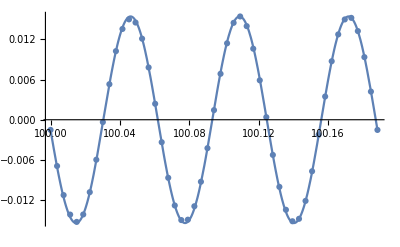

```mathematica
testFitting[beqsM[100],{ϕ1,ϕ2},{σ,100},100]
```

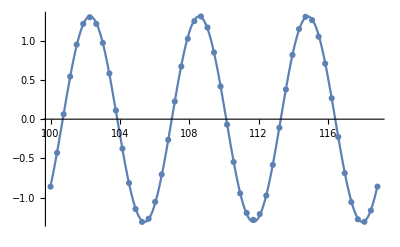

```mathematica
testFitting[feqsM[1],{ψ1,ψ2},{σ,100},1]
```

### Generate and export numeric data

```mathematica
Clear[ϵ,pRange,min]
```

```mathematica
ϵ=0.000001;
(*pRange=Join[Range[0.1,10,0.1],Range[12,100,2]];*) (* much faster with this range, 31s in total, when min=100 *)
pRange=Range[0.1,50,0.1]; (* 1090s for min = 1000, 120s min=100*)
min=1000;

Timing[
dataYp=pPhaseTable[beqsP[p],{ϕ1,ϕ2},{σ,min},{p,pRange}];
dataFp=pPhaseTable[feqsP[p],{ψ1,ψ2},{σ,min},{p,pRange}];
dataYm=pPhaseTable[beqsM[p],{ϕ1,ϕ2},{σ,min},{p,pRange}];
dataFm=pPhaseTable[feqsM[p],{ψ1,ψ2},{σ,min},{p,pRange}];
]
```

{1098.68,Null}

#### Export numeric data

```mathematica
dataExport[ans_,name_?StringQ]:=Export[NotebookDirectory[]<>"DataPhaseShifts/"<>name<>".dat",ans, "Data"];
(*Note that we must create first the folder "DataPhaseShifts/", either by hand or using CreateDirectory["DataPhaseShifts"]*)

(* We should save each components separately in order to have the right format for the import, namely, just numbers, no parenthesis. *)
dataExport[dataYp[[1]],"dataYp1L"];
dataExport[dataYp[[2]],"dataYp2L"];
dataExport[dataYm[[1]],"dataYm1L"];
dataExport[dataYm[[2]],"dataYm2L"];
dataExport[dataFp[[1]],"dataFp1L"];
dataExport[dataFp[[2]],"dataFp2L"];
dataExport[dataFm[[1]],"dataFm1L"];
dataExport[dataFm[[2]],"dataFm2L"];
```

### Study data set with σmin=100

#### Import numeric data

```mathematica
folder="DataPhaseShifts/";
dataYp1=Import[NotebookDirectory[]<>folder<>"dataYp1.dat","Table"];
dataYm1=Import[NotebookDirectory[]<>folder<>"dataYm1.dat","Table"];
dataFp1=Import[NotebookDirectory[]<>folder<>"dataFp1.dat","Table"];
dataFm1=Import[NotebookDirectory[]<>folder<>"dataFm1.dat","Table"];
dataYp2=Import[NotebookDirectory[]<>folder<>"dataYp2.dat","Table"];
dataYm2=Import[NotebookDirectory[]<>folder<>"dataYm2.dat","Table"];
dataFp2=Import[NotebookDirectory[]<>folder<>"dataFp2.dat","Table"];
dataFm2=Import[NotebookDirectory[]<>folder<>"dataFm2.dat","Table"];
Clear[folder]
```

#### Phase-shifts comparisons

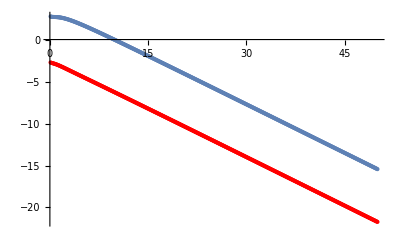
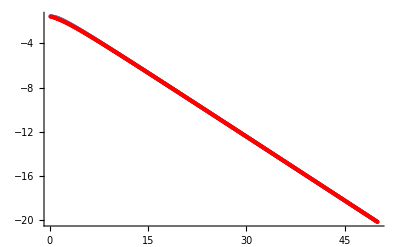

```mathematica
(* there should be no constant difference between the 1st components, up to multiples of pi, where odd pi is due to a sign in the amplitude *)
{Show[ListPlot[dataYp1, PlotRange->{{0,20},{5,-10}}],ListPlot[dataFp1,PlotStyle->Red]],
Show[ListPlot[dataYm1, PlotRange->{{0,20},{0,-10}}],ListPlot[dataFm1,PlotStyle->Red]]}
```

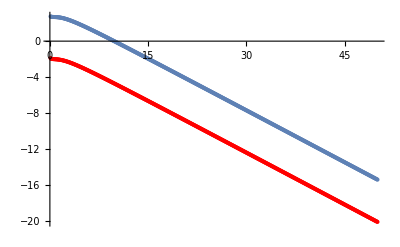
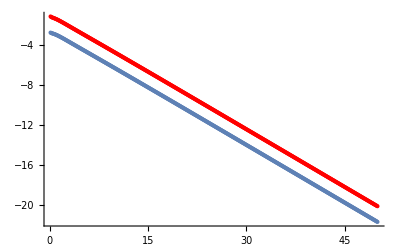
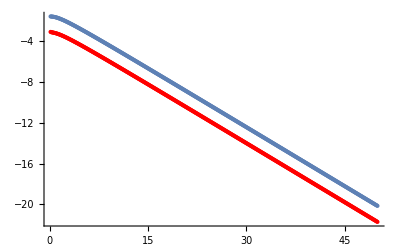
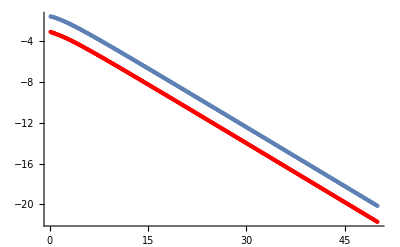

```mathematica
(* odd π/2 shift difference between 1st and 2nd components *)
{Show[ListPlot[dataYp1, PlotRange->{{0,20},{5,-10}}],ListPlot[dataYp2,PlotStyle->Red]],
Show[ListPlot[dataFp1, PlotRange->{{0,20},{2,-10}}],ListPlot[dataFp2,PlotStyle->Red]],
Show[ListPlot[dataYm1, PlotRange->{{0,20},{2,-10}}],ListPlot[dataYm2,PlotStyle->Red]],
Show[ListPlot[dataFm1, PlotRange->{{0,20},{2,-10}}],ListPlot[dataFm2,PlotStyle->Red]]}
```

#### Numeric integration

The expected result is 1.

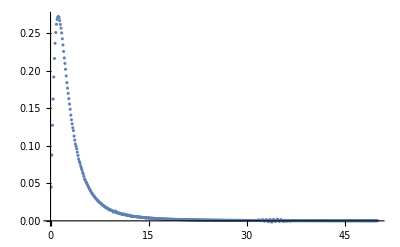

```mathematica
dataIntegrand=Transpose@{dataYp1[[;;,1]],1/2 4 4 1/π 4/9 dataYp1[[;;,1]]/(√(4/9 dataYp1[[;;,1]]^2+1))1/2(dataFp1[[;;,2]]+dataFm1[[;;,2]]-dataYp1[[;;,2]]-dataYm1[[;;,2]]+2π)};
ListPlot[dataIntegrand,PlotRange->All]
```

Integration by summation:

```mathematica
Table[
0.1Sum[dataIntegrand[[;;,2]][[i]],{i,1,imax}],
{imax,300,500,100}]
```

{1.00941,1.01291,1.01448}

Using interpolation for integration:

```mathematica
Table[
NIntegrate[Interpolation[dataIntegrand][p],{p,0.1,pmax}],
{pmax,30,50,10}]
```

{1.00749,1.011,1.01257}

### Study data set with σmin=1000

#### Import numeric data

```mathematica
folder="DataPhaseShifts/";
dataYp1=Import[NotebookDirectory[]<>folder<>"dataYp1L.dat","Table"];
dataYm1=Import[NotebookDirectory[]<>folder<>"dataYm1L.dat","Table"];
dataFp1=Import[NotebookDirectory[]<>folder<>"dataFp1L.dat","Table"];
dataFm1=Import[NotebookDirectory[]<>folder<>"dataFm1L.dat","Table"];
dataYp2=Import[NotebookDirectory[]<>folder<>"dataYp2L.dat","Table"];
dataYm2=Import[NotebookDirectory[]<>folder<>"dataYm2L.dat","Table"];
dataFp2=Import[NotebookDirectory[]<>folder<>"dataFp2L.dat","Table"];
dataFm2=Import[NotebookDirectory[]<>folder<>"dataFm2L.dat","Table"];
Clear[folder]
```

#### Phase-shifts comparisons

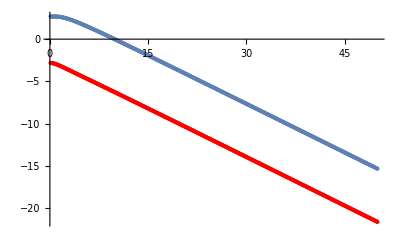
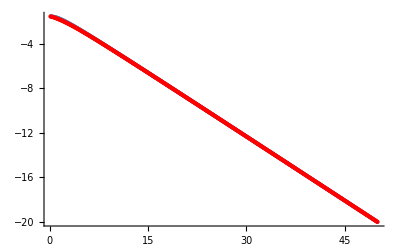

```mathematica
(* there should be no constant difference between the 1st components, up to multiples of pi, where odd pi is due to a sign in the amplitude *)
{Show[ListPlot[dataYp1, PlotRange->{{0,20},{5,-10}}],ListPlot[dataFp1,PlotStyle->Red]],
Show[ListPlot[dataYm1, PlotRange->{{0,20},{0,-10}}],ListPlot[dataFm1,PlotStyle->Red]]}
```

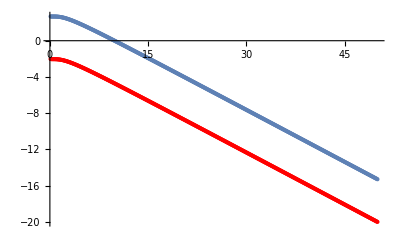
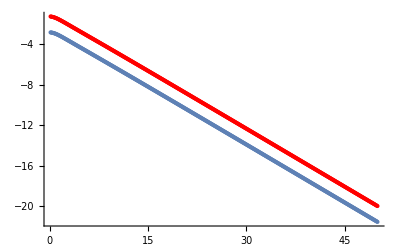
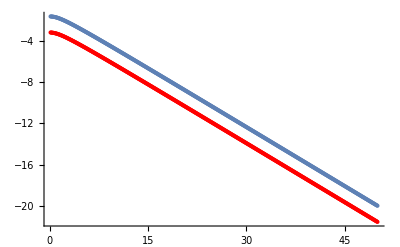
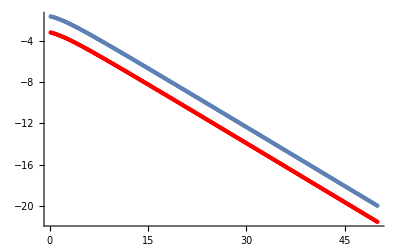

```mathematica
(* odd π/2 shift difference between 1st and 2nd components *)
{Show[ListPlot[dataYp1, PlotRange->{{0,20},{5,-10}}],ListPlot[dataYp2,PlotStyle->Red]],
Show[ListPlot[dataFp1, PlotRange->{{0,20},{2,-10}}],ListPlot[dataFp2,PlotStyle->Red]],
Show[ListPlot[dataYm1, PlotRange->{{0,20},{2,-10}}],ListPlot[dataYm2,PlotStyle->Red]],
Show[ListPlot[dataFm1, PlotRange->{{0,20},{2,-10}}],ListPlot[dataFm2,PlotStyle->Red]]}
```

#### Comparison with WKB

WKB prediction for individual phase-shifts (see WKB section):
	δ(p)=-0.384p+ 0.785-1.32 p^-1+O(p^-2)

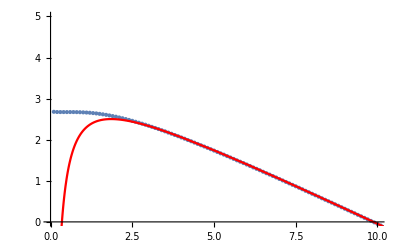

```mathematica
Show[ListPlot[dataYp1,PlotRange->{{0,10},{0,5}}],Plot[-0.384p+ 0.785-1.32/p+π,{p,0,50},PlotStyle->Red]]
```

For the difference phase-shifts:
	δ_(F+)+δ_(F-)-δ_(B+)-δ_(B-)=17 p^-3+140 p^-5+O(p^-7)

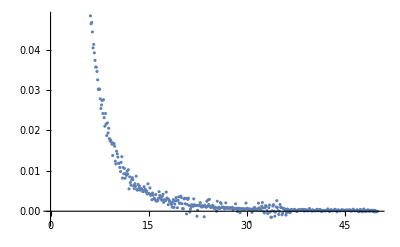

```mathematica
diff=Transpose@{dataFp1[[;;,1]],dataFp1[[;;,2]]+dataFm1[[;;,2]]-dataYp1[[;;,2]]-dataYm1[[;;,2]]+2π};
ListPlot@diff
```

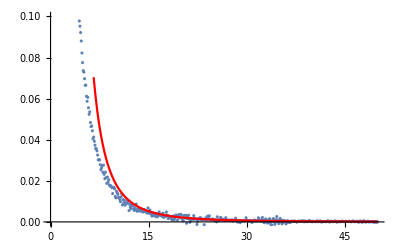

```mathematica
Show[ListPlot[diff,PlotRange->{{0,50},{0,0.1}}],Plot[17/p^3+140/p^5,{p,0,50},PlotStyle->Red]]
```

#### Numeric integration

The expected result is 1.

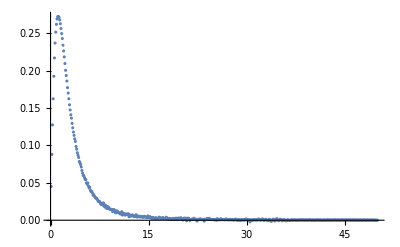

```mathematica
dataIntegrand=Transpose@{dataYp1[[;;,1]],1/2 4 4 1/π 4/9 dataYp1[[;;,1]]/(√(4/9 dataYp1[[;;,1]]^2+1))1/2(dataFp1[[;;,2]]+dataFm1[[;;,2]]-dataYp1[[;;,2]]-dataYm1[[;;,2]]+2π)};
ListPlot[dataIntegrand,PlotRange->All]
```

Integration by summation:

```mathematica
Table[
0.1Sum[dataIntegrand[[;;,2]][[i]],{i,1,imax}],
{imax,300,500,100}]
```

{1.01034,1.01311,1.0146}

Using interpolation for integration:

```mathematica
Table[
NIntegrate[Interpolation[dataIntegrand][p],{p,0.1,pmax}],
{pmax,30,50,10}]
```

{1.00843,1.01122,1.01271}

##### With second fermionic components

If we consider 2nd fermionic components instead, the result is worse, because 2nd components have 1/σ correction earlier than the first (see their asymptotics).

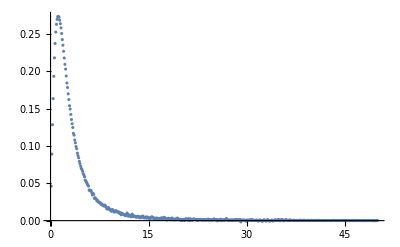

{1.01214,1.01605,1.01793}

```mathematica
dataIntegrand=Transpose@{dataYp1[[;;,1]],1/2 4 4 1/π 4/9 dataYp1[[;;,1]]/(√(4/9 dataYp1[[;;,1]]^2+1))1/2(dataFp2[[;;,2]]+dataFm2[[;;,2]]-dataYp1[[;;,2]]-dataYm1[[;;,2]]+2π)};
ListPlot[dataIntegrand,PlotRange->All]
Table[
NIntegrate[Interpolation[dataIntegrand][p],{p,0.1,pmax}],
{pmax,30,50,10}]
```

#### Numeric error

Error coming from numeric integration and WKB tail:

```mathematica
dp=0.1;
σmax=1000;
pmax=50;
n=pmax*10;
dp √Sum[(1/2 4 4 4/9 1/π(i dp)/(√(4/9(i dp)^2+1))1/2 2 (3 i dp)/(10 σmax))^2,{i,1,n}]
Assuming[pmax>0,Integrate[1/2 4 4 4/9 1/π p/(√(4/9(p)^2+1))1/2 17.2856/p^3,{p,pmax,∞}]] (* WKB tail error *)
%+%%
Clear[dp,σmax,pmax,n]
```

0.0328819

0.00293383

0.0358157